## Part XX

```mathematica
Quit
```

Covariant equations

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

$CommuteCovDsOnScalars=True;
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];

DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";


DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]

(* We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^* *)

DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],CD[a][Phi[]]CD[-a][PhiC[]]]

DefTensor[XR[],M4,PrintAs->"X"]
IndexSet[XR[],CD[a][Phi[]]CD[-a][Phi[]]]


(*DefScalarFunction[V]*)
DefConstantSymbol[ka, PrintAs ->"k"]
DefConstantSymbol[alpha, PrintAs ->"α"]
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[L1, PrintAs ->"λ_1"]
```

(▽_a φ^*) (▽^a φ)

(▽_a φ) (▽^a φ)

```mathematica
(* Lagrangian *)
```

La definición usada es, arXiv:1404.6495v3

L_2=G_2(ϕ,X)=-λ_1 m^2 ϕ^2-α X,
L_3=G_3(ϕ,X)\Box[ϕ]=0, 
G_3=G_5=L_5=0
G_4(ϕ,X) =(k-η/2 X X) .... signo menos y 1/2, sinó no da bien los signos relativos y nos queda 2 η
L_4=G_4(ϕ,X) R -2G_(4,X)(ϕ,X)[(\Box(ϕ))^2-ϕ^ab ϕ_ab]+F_4(ϕ,X)(e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c'),
L_4= (k-η/2 XX) R+2η X [(\Box(ϕ))^2-ϕ^ab ϕ_ab]-2η  (e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c')
F_4(ϕ,X)=(2 G_(4,X))/X=-2η 
\Box(ϕ)=∇_a ∇^a ϕ

```mathematica
RHS=2*eta*XR[]*(CD[-b]@CD[b]@Phi[]*CD[-a]@CD[a]@Phi[]-CD[-a]@CD[-b]@Phi[]*CD[a]@CD[b]@Phi[])-2eta*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-e][Phi[]]*CD[-a][Phi[]]*CD[-c][CD[-g][Phi[]]]*CD[-b][CD[-f][Phi[]]])//ContractMetric//ToCanonical//Simplification
```

4 η (▽^a φ) ((▽_a φ) (-(▽^b▽^c φ) (▽_c▽_b φ)+(▽_b▽^b φ) (▽_c▽^c φ))+(-(▽_b▽^b φ) (▽_c▽_a φ)+(▽^b▽_a φ) (▽_c▽_b φ)) (▽^c φ))

```mathematica
L=Sqrt[-Detmetric[]]*(-L1*mS^2*Phi[]*PhiC[]-alpha*X[]+(ka-eta/2*X[]*X[])*RicciScalarCD[]+2*eta*X[]*(CD[-b]@CD[b]@Phi[]*CD[-a]@CD[a]@PhiC[]-CD[-a]@CD[-b]@Phi[]*CD[a]@CD[b]@PhiC[])-2eta*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-e][Phi[]]*CD[-a][PhiC[]]*CD[-c][CD[-g][Phi[]]]*CD[-b][CD[-f][PhiC[]]]))
```

√(-g^OverTilde[~]) (-λ_1 m^2 φ φ^*-α (▽_d φ^*) (▽^d φ)-2 η (g | a | g
  |   g | b | f
  |   g | c | e
  |  -g | a | f
  |   g | b | g
  |   g | c | e
  |  -g | a | g
  |   g | b | e
  |   g | c | f
  |  +g | a | e
  |   g | b | g
  |   g | c | f
  |  +g | a | f
  |   g | b | e
  |   g | c | g
  |  -g | a | e
  |   g | b | f
  |   g | c | g
  |  ) (▽_a φ^*) (▽_e φ) (▽_f▽_b φ^*) (▽_g▽_c φ)+R[▽] (k-1/2 η (▽_h φ^*) (▽^h φ) (▽_i φ^*) (▽^i φ))+2 η (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ)) (▽_j φ^*) (▽^j φ))

```mathematica
L=Sqrt[-Detmetric[]]*(-L1*mS^2*PhiC[]*Phi[]-alpha*X[]+(ka-eta/2*X[]*X[])*RicciScalarCD[]+2*eta*X[]*(CD[-a]@CD[a]@PhiC[]*CD[-b]@CD[b]@Phi[]-CD[a]@CD[b]@PhiC[]*CD[-a]@CD[-b]@Phi[])-2eta*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][PhiC[]]*CD[-e][Phi[]]*CD[-b][CD[-f][PhiC[]]]*CD[-c][CD[-g][Phi[]]]))
```

√(-g^OverTilde[~]) (-λ_1 m^2 φ φ^*-α (▽_d φ^*) (▽^d φ)-2 η (g | a | g
  |   g | b | f
  |   g | c | e
  |  -g | a | f
  |   g | b | g
  |   g | c | e
  |  -g | a | g
  |   g | b | e
  |   g | c | f
  |  +g | a | e
  |   g | b | g
  |   g | c | f
  |  +g | a | f
  |   g | b | e
  |   g | c | g
  |  -g | a | e
  |   g | b | f
  |   g | c | g
  |  ) (▽_a φ^*) (▽_e φ) (▽_f▽_b φ^*) (▽_g▽_c φ)+R[▽] (k-1/2 η (▽_h φ^*) (▽^h φ) (▽_i φ^*) (▽^i φ))+2 η (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ)) (▽_j φ^*) (▽^j φ))

```mathematica
Lpert=ToCanonical@ContractMetric@ExpandPerturbation@Perturbation@L//NoScalar;
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=-(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification;
```

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //RicciToEinstein//Simplification //ContractMetric
```

λ_1 m^2 φ^*-α (▽_a▽^a φ^*)-3 η R[▽] (▽_a φ^*) (▽^a φ^*) (▽_b▽^b φ)-3 η R[▽] (▽_a φ^*) (▽^a φ) (▽_b▽^b φ^*)+3 η R[▽] (▽^a φ^*) (▽_b▽_a φ) (▽^b φ^*)+3 η R[▽] (▽^a φ) (▽_b▽_a φ^*) (▽^b φ^*)+6 η G[▽] |   | c
b |   (▽^a φ) (▽^b φ^*) (▽_c▽_a φ^*)+8 η G[▽] |   | c
a |   (▽^a φ^*) (▽^b φ^*) (▽_c▽_b φ)+4 η G[▽] | b | c
  |   (▽_a φ^*) (▽^a φ) (▽_c▽_b φ^*)+2 η G[▽] |   | c
a |   (▽^a φ) (▽^b φ^*) (▽_c▽_b φ^*)-6 η G[▽] |   |  
a | b (▽^a φ^*) (▽^b φ^*) (▽_c▽^c φ)+6 η (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)-8 η G[▽] |   |  
a | b (▽^a φ) (▽^b φ^*) (▽_c▽^c φ^*)-14 η (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)+2 η (▽^a φ^*) (▽_b▽^b φ) (▽_c▽^c▽_a φ^*)-2 η (▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ^*)-2 η (▽^a φ) (▽^b φ^*) (▽_c G[▽] |   |  
a | b) (▽^c φ^*)+12 η (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)-2 η (▽^a φ^*) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ)-4 η (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)+2 η (▽^a φ) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ^*)+6 η R[▽] |   |   |   |  
a | c | b | d (▽^a φ^*) (▽^b φ^*) (▽^d▽^c φ)+6 η R[▽] |   |   |   |  
a | c | b | d (▽^a φ) (▽^b φ^*) (▽^d▽^c φ^*)

We obtained the coefficients

```mathematica
(*Ecuϕ-alpha Coefficient[Ecuϕ,alpha]-eta Coefficient[Ecuϕ,eta]//Simplification
Coefficient[Ecuϕ,alpha]
Coefficient[Ecuϕ,eta]*)
```

Checking if is equal to when is considerate the scalar field real

```mathematica
(*
Ecuϕ/.PhiC[]-> Phi[]//ToCanonical//Simplify;
Collect[%, {alpha, eta},Simplify]
*)
```

And here is the tensor equation of motion. We vary with respect to g^ab.

```mathematica
RHS=-VarD[metpert[LI[1],a,b],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical;(*//Simplification//Simplify;*)
```

```mathematica
Ecu=ContractMetric[SortCovDs[RHS,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical (*//RicciToEinstein//Simplification*);
```

```mathematica
Ecu=Collect[Ecu, {alpha, eta},Simplify]
```

k G[▽] |   |  
a | b+1/2 λ_1 m^2 g |   |  
a | b φ φ^*+1/2 α (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (▽_c φ^*) (▽^c φ))+1/2 η (-4 (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ)-3 (▽_b φ^*) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽^d φ)-5 (▽_b φ^*) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽^d φ)-2 (▽_b φ) (▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)-4 (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ^*)-2 (▽_b φ^*) (▽_c▽_a φ) (▽^c φ) (▽_d▽^d φ^*)-5 (▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽^d φ^*)-3 (▽_b φ) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽^d φ^*)+4 R[▽] |   |  
a | d (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ)-G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ) (▽_d φ^*) (▽^d φ)+4 (▽_c▽_a φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ)-2 (▽_c φ^*) (▽^c φ) (▽_d▽_b▽_a φ^*) (▽^d φ)-4 (▽_b▽_a φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ)+(▽_b φ^*) (▽^c φ) (▽_d▽_c▽_a φ^*) (▽^d φ)+4 R[▽] |   |  
a | d (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*)+2 (▽_c▽_b φ^*) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*)+2 (▽_c▽_b φ) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ^*)+2 (▽_c▽_a φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*)+4 (▽_c▽_a φ) (▽^c φ^*) (▽_d▽_b φ) (▽^d φ^*)+2 (▽_c▽_a φ) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ^*)-2 (▽_c φ^*) (▽^c φ) (▽_d▽_b▽_a φ) (▽^d φ^*)-4 (▽_b▽_a φ^*) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*)-4 (▽_b▽_a φ) (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*)-4 (▽_b▽_a φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*)+(▽_b φ^*) (▽^c φ) (▽_d▽_c▽_a φ) (▽^d φ^*)+(▽_b φ) (▽^c φ^*) (▽_d▽_c▽_a φ) (▽^d φ^*)+(▽_b φ) (▽^c φ) (▽_d▽_c▽_a φ^*) (▽^d φ^*)+2 (▽_c φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d▽_a φ)+5 (▽_b φ^*) (▽^c φ^*) (▽_d▽_c φ) (▽^d▽_a φ)+4 (▽_b φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_a φ)+3 (▽_b φ) (▽^c φ^*) (▽_d▽_c φ^*) (▽^d▽_a φ)+5 (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)+2 (▽_c φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d▽_b φ)+3 (▽_b φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d▽_c φ)+4 (▽_b φ) (▽^c φ^*) (▽_d▽_a φ^*) (▽^d▽_c φ)+4 g |   |  
a | b (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ)+4 g |   |  
a | b (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ)+4 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽_d▽^d φ) (▽_e▽^e φ^*)+4 g |   |  
a | b (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽^e φ^*)+4 g |   |  
a | b (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)+2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽^e▽_d φ)+2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽^e▽_d φ^*)-R[▽] |   |   |   |  
a | c | d | e (▽_b φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)-8 g |   |  
a | b R[▽] |   |  
d | e (▽_c φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)+2 R[▽] |   |   |   |  
a | d | b | e (▽_c φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)+2 R[▽] |   |   |   |  
a | e | b | d (▽_c φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)+2 R[▽] |   |   |   |  
a | d | c | e (▽_b φ) (▽^c φ) (▽^d φ^*) (▽^e φ^*)-2 g |   |  
a | b (▽^c φ) (▽^d φ^*) (▽_e▽_d▽_c φ) (▽^e φ^*)-2 g |   |  
a | b (▽^c φ) (▽^d φ) (▽_e▽_d▽_c φ^*) (▽^e φ^*)-(▽_a φ^*) (3 (▽_c▽_b φ^*) (▽^c φ) (▽_d▽^d φ)+5 (▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d φ)+2 (▽_c▽_b φ) (▽^c φ) (▽_d▽^d φ^*)-4 R[▽] |   |  
b | d (▽_c φ^*) (▽^c φ) (▽^d φ)-(▽^c φ) (▽_d▽_c▽_b φ^*) (▽^d φ)-(▽^c φ) (▽_d▽_c▽_b φ) (▽^d φ^*)-5 (▽^c φ^*) (▽_d▽_c φ) (▽^d▽_b φ)-4 (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_b φ)-3 (▽^c φ) (▽_d▽_b φ^*) (▽^d▽_c φ)+(▽_b φ^*) (-2 (▽_c▽^c φ) (▽_d▽^d φ)+2 R[▽] |   |  
c | d (▽^c φ) (▽^d φ)+2 (▽_d▽_c φ) (▽^d▽^c φ))+(▽_b φ) (R[▽] (▽_c φ^*) (▽^c φ)-4 (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽^c φ^*) (▽_d▽^d▽_c φ)+(▽^c φ) (▽_d▽^d▽_c φ^*)+6 (▽_d▽_c φ^*) (▽^d▽^c φ))+R[▽] |   |   |   |  
b | c | d | e (▽^c φ) (▽^d φ) (▽^e φ^*))+(▽_a φ) (2 (▽_b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)-3 (▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d φ^*)-(▽_c▽_b φ^*) (2 (▽^c φ^*) (▽_d▽^d φ)+5 (▽^c φ) (▽_d▽^d φ^*))+4 R[▽] |   |  
b | d (▽_c φ^*) (▽^c φ) (▽^d φ^*)-2 R[▽] |   |  
c | d (▽_b φ) (▽^c φ^*) (▽^d φ^*)+(▽^c φ^*) (▽_d▽_c▽_b φ) (▽^d φ^*)+(▽^c φ) (▽_d▽_c▽_b φ^*) (▽^d φ^*)+3 (▽^c φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ)+5 (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+4 (▽^c φ^*) (▽_d▽_b φ^*) (▽^d▽_c φ)-(▽_b φ^*) (R[▽] (▽_c φ^*) (▽^c φ)-4 (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽^c φ^*) (▽_d▽^d▽_c φ)+(▽^c φ) (▽_d▽^d▽_c φ^*)+6 (▽_d▽_c φ^*) (▽^d▽^c φ))-2 (▽_b φ) (▽_d▽_c φ^*) (▽^d▽^c φ^*)+2 R[▽] |   |   |   |  
b | d | c | e (▽^c φ) (▽^d φ^*) (▽^e φ^*))-4 g |   |  
a | b (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)-6 g |   |  
a | b (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)-4 g |   |  
a | b (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)-6 g |   |  
a | b (▽^c φ) (▽^d φ^*) (▽_e▽_c φ^*) (▽^e▽_d φ)-2 g |   |  
a | b R[▽] |   |   |   |  
c | e | d | f (▽^c φ) (▽^d φ) (▽^e φ^*) (▽^f φ^*))

```mathematica
(*Ecu-alpha Coefficient[Ecu,alpha]-eta Coefficient[Ecu,eta]
Coefficient[Ecu,alpha]
Coefficient[Ecu,eta]*)
```

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]

MetricCompute[metric,esf,All,CVSimplify->Simplify]

DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]

(* Next,we need to set the scalar to be ϕ=φ(r)Exp[-iwt] *)
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
(*Because xCoba only work with down indices, is neccesary change the up-indice for down-indices*)
```

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];

ImplodedTensorValues[CD,EinsteinCD,esf];
ChangeComponents[EinsteinCD[a,b]//ToBasis[esf],EinsteinCD[-a, -b]//ToBasis[esf]];

ChangeComponents[CDEinsteinCD[a,b,c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[a,b,-c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[a,-b,- c]//ToBasis[esf],CDEinsteinCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,-b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,b, -c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDEinsteinCD[-a,-b, c]//ToBasis[esf],CDEinsteinCD[-a, -b, -c]//ToBasis[esf]];
```

Computed ▽φ | a
 →▽φ |  
b g | a | b
  |   in 0.01258 Seconds

Computed ▽▽φ |   | b
a |  →▽▽φ |   |  
a | c g | b | c
  |   in 0.098145 Seconds

Computed ▽▽φ | a | b
  |  →▽▽φ |   | b
c |   g | a | c
  |   in 0.11677 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.365723 Seconds

Computed ▽▽▽φ |   | b | c
a |   |  →▽▽▽φ |   |   | c
a | d |   g | b | d
  |   in 0.702532 Seconds

Computed ▽▽▽φ | a | b | c
  |   |  →▽▽▽φ |   | b | c
d |   |   g | a | d
  |   in 0.661392 Seconds

Computed ▽▽▽φ |   | b |  
a |   | c→▽▽▽φ |   |   |  
a | d | c g | b | d
  |   in 0.818073 Seconds

Computed ▽▽▽φ | a | b |  
  |   | c→▽▽▽φ |   | b |  
d |   | c g | a | d
  |   in 0.635204 Seconds

Computed ▽▽▽φ | a |   |  
  | b | c→▽▽▽φ |   |   |  
d | b | c g | a | d
  |   in 0.524224 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.651156 Seconds

Computed ▽▽▽φ |   | b | c
a |   |  →▽▽▽φ |   |   | c
a | d |   g | b | d
  |   in 0.473613 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.492794 Seconds

Computed ▽▽▽φ |   | b |  
a |   | c→▽▽▽φ |   |   |  
a | d | c g | b | d
  |   in 0.544063 Seconds

Computed ▽▽▽φ |   |   | c
a | b |  →▽▽▽φ |   |   |  
a | b | d g | c | d
  |   in 0.476042 Seconds

Computed ▽φ^* | a
 →▽φ^* |  
b g | a | b
  |   in 0.01826 Seconds

Computed ▽▽φ^* |   | b
a |  →▽▽φ^* |   |  
a | c g | b | c
  |   in 0.12588 Seconds

Computed ▽▽φ^* | a | b
  |  →▽▽φ^* |   | b
c |   g | a | c
  |   in 0.094837 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.31763 Seconds

Computed ▽▽▽φ^* |   | b | c
a |   |  →▽▽▽φ^* |   |   | c
a | d |   g | b | d
  |   in 0.69162 Seconds

Computed ▽▽▽φ^* | a | b | c
  |   |  →▽▽▽φ^* |   | b | c
d |   |   g | a | d
  |   in 0.642853 Seconds

Computed ▽▽▽φ^* |   | b |  
a |   | c→▽▽▽φ^* |   |   |  
a | d | c g | b | d
  |   in 0.862428 Seconds

Computed ▽▽▽φ^* | a | b |  
  |   | c→▽▽▽φ^* |   | b |  
d |   | c g | a | d
  |   in 0.737182 Seconds

Computed ▽▽▽φ^* | a |   |  
  | b | c→▽▽▽φ^* |   |   |  
d | b | c g | a | d
  |   in 0.524365 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.462941 Seconds

Computed ▽▽▽φ^* |   | b | c
a |   |  →▽▽▽φ^* |   |   | c
a | d |   g | b | d
  |   in 0.46751 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.449042 Seconds

Computed ▽▽▽φ^* |   | b |  
a |   | c→▽▽▽φ^* |   |   |  
a | d | c g | b | d
  |   in 0.471008 Seconds

Computed ▽▽▽φ^* |   |   | c
a | b |  →▽▽▽φ^* |   |   |  
a | b | d g | c | d
  |   in 0.464969 Seconds

Computed ▽R[▽] | a
 →▽R[▽] |  
b g | a | b
  |   in 0.01694 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.26143 Seconds

Computed ▽R[▽] |   | b | c
a |   |  →▽R[▽] |   |   | c
a | d |   g | b | d
  |   in 0.5114 Seconds

Computed ▽R[▽] | a | b | c
  |   |  →▽R[▽] |   | b | c
d |   |   g | a | d
  |   in 0.431467 Seconds

Computed ▽R[▽] |   | b |  
a |   | c→▽R[▽] |   |   |  
a | d | c g | b | d
  |   in 0.664187 Seconds

Computed ▽R[▽] | a | b |  
  |   | c→▽R[▽] |   | b |  
d |   | c g | a | d
  |   in 0.505823 Seconds

Computed ▽R[▽] | a |   |  
  | b | c→▽R[▽] |   |   |  
d | b | c g | a | d
  |   in 0.468862 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.407308 Seconds

Computed ▽R[▽] |   | b | c
a |   |  →▽R[▽] |   |   | c
a | d |   g | b | d
  |   in 0.381848 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.405221 Seconds

Computed ▽R[▽] |   | b |  
a |   | c→▽R[▽] |   |   |  
a | d | c g | b | d
  |   in 0.438653 Seconds

Computed ▽R[▽] |   |   | c
a | b |  →▽R[▽] |   |   |  
a | b | d g | c | d
  |   in 0.396434 Seconds

Computed R[▽] |   | b
a |  →g | b | c
  |   R[▽] |   |  
a | c in 0.094186 Seconds

Computed R[▽] | a | b
  |  →g | a | c
  |   R[▽] |   | b
c |   in 0.074214 Seconds

Computed G[▽] |   | b
a |  →G[▽] |   |  
a | c g | b | c
  |   in 0.074389 Seconds

Computed G[▽] | a | b
  |  →G[▽] |   | b
c |   g | a | c
  |   in 0.075103 Seconds

Computed ▽G[▽] |   |   | c
a | b |  →▽G[▽] |   |   |  
a | b | d g | c | d
  |   in 0.2225 Seconds

Computed ▽G[▽] |   | b | c
a |   |  →▽G[▽] |   |   | c
a | d |   g | b | d
  |   in 0.3382 Seconds

Computed ▽G[▽] | a | b | c
  |   |  →▽G[▽] |   | b | c
d |   |   g | a | d
  |   in 0.33559 Seconds

Computed ▽G[▽] |   | b |  
a |   | c→▽G[▽] |   |   |  
a | d | c g | b | d
  |   in 0.513744 Seconds

Computed ▽G[▽] | a | b |  
  |   | c→▽G[▽] |   | b |  
d |   | c g | a | d
  |   in 0.429298 Seconds

Computed ▽G[▽] | a |   |  
  | b | c→▽G[▽] |   |   |  
d | b | c g | a | d
  |   in 0.414086 Seconds

Computed ▽G[▽] |   |   | c
a | b |  →▽G[▽] |   |   |  
a | b | d g | c | d
  |   in 0.377232 Seconds

Computed ▽G[▽] |   | b | c
a |   |  →▽G[▽] |   |   | c
a | d |   g | b | d
  |   in 0.435562 Seconds

Computed ▽G[▽] |   |   | c
a | b |  →▽G[▽] |   |   |  
a | b | d g | c | d
  |   in 0.403503 Seconds

Computed ▽G[▽] |   | b |  
a |   | c→▽G[▽] |   |   |  
a | d | c g | b | d
  |   in 0.398154 Seconds

Computed ▽G[▽] |   |   | c
a | b |  →▽G[▽] |   |   |  
a | b | d g | c | d
  |   in 0.37749 Seconds

If we want to see these values, we first need to put it in the appropriate basis, and then ask xCoba to substitute in the appropriate value. Note that you may need to use ToValues multiple times.

```mathematica
RicciScalarCD[]//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Expand
```

2/r^2-2/(gg[r]^2 r^2)+(4 gg'[r])/(gg[r]^3 r)-(4 NN'[r])/(gg[r]^2 NN[r] r)+(2 gg'[r] NN'[r])/(gg[r]^3 NN[r])-(2 NN''[r])/(gg[r]^2 NN[r])

```mathematica
Hesfϕ=Ecuϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//Simplify
```

1/(gg[r]^7 NN[r]^6 r^2)ⅇ^(-ⅈ w t) (gg[r]^7 NN[r]^2 ϕ[r] (-α w^2 NN[r]^2 r^2+λ_1 m^2 NN[r]^4 r^2+2 η w^4 ϕ[r]^2)-70 η NN[r]^5 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^3+gg[r]^4 NN[r] gg'[r] (4 η w^4 r^2 ϕ[r]^3 NN'[r]+α NN[r]^5 r^2 ϕ'[r]-2 η w^2 NN[r]^3 ϕ[r]^2 ϕ'[r]+4 η w^4 NN[r] r ϕ[r]^2 (ϕ[r]-2 r ϕ'[r]))-gg[r]^5 (-16 η w^4 r^2 ϕ[r]^3 NN'[r]^2+α NN[r]^5 r^2 NN'[r] ϕ'[r]+2 η w^2 NN[r]^3 ϕ[r]^2 NN'[r] ϕ'[r]+4 η w^4 NN[r] r ϕ[r]^2 (6 r NN'[r] ϕ'[r]+ϕ[r] (2 NN'[r]+r NN''[r]))+α NN[r]^6 r (2 ϕ'[r]+r ϕ''[r])-2 η w^2 NN[r]^4 ϕ[r] (ϕ'[r]^2+ϕ[r] ϕ''[r])+2 η w^4 NN[r]^2 ϕ[r] (ϕ[r]^2-4 r^2 ϕ'[r]^2-4 r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+2 η gg[r] NN[r]^4 ϕ'[r] (8 w^2 r ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+3 NN[r] ϕ''[r]+3 NN'[r] (ϕ'[r]+2 r ϕ''[r])))+2 η gg[r]^2 NN[r]^3 (3 NN[r]^3 gg'[r] ϕ'[r]^3+2 w^2 r ϕ[r] gg'[r] NN'[r] ϕ'[r] (13 ϕ[r]+3 r ϕ'[r])+w^2 NN[r] (-68 r ϕ[r] gg'[r] ϕ'[r]^2-8 r^2 gg'[r] ϕ'[r]^3+ϕ[r]^2 (-2 r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]-2 r ϕ''[r]))))-2 η gg[r]^3 NN[r]^2 (NN[r]^3 NN'[r] ϕ'[r]^3-4 w^2 r ϕ[r] NN'[r]^2 ϕ'[r] (4 ϕ[r]+r ϕ'[r])+3 NN[r]^4 ϕ'[r]^2 ϕ''[r]+w^2 NN[r]^2 (ϕ[r]^2 ϕ''[r]-4 r ϕ'[r]^2 (5 ϕ'[r]+2 r ϕ''[r])-ϕ[r] ϕ'[r] (21 ϕ'[r]+44 r ϕ''[r]))+w^2 NN[r] (4 r^2 NN'[r] ϕ'[r]^3+2 r ϕ[r] ϕ'[r] (r ϕ'[r] NN''[r]+NN'[r] (17 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 (8 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+8 r ϕ''[r])))))

```mathematica
eqϕ=Collect[Hesfϕ*gg[r]^7 NN[r]^6 r^2*ⅇ^(ⅈ w t),{alpha,eta}, Simplify]
```

λ_1 m^2 gg[r]^7 NN[r]^6 r^2 ϕ[r]+α gg[r]^4 NN[r]^4 r (-w^2 gg[r]^3 r ϕ[r]+NN[r]^2 r gg'[r] ϕ'[r]-gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 η (w^4 gg[r]^7 NN[r]^2 ϕ[r]^3-35 NN[r]^5 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^3+w^2 gg[r]^4 NN[r] ϕ[r]^2 gg'[r] (2 w^2 r^2 ϕ[r] NN'[r]-NN[r]^3 ϕ'[r]+2 w^2 NN[r] r (ϕ[r]-2 r ϕ'[r]))+w^2 gg[r]^5 ϕ[r] (8 w^2 r^2 ϕ[r]^2 NN'[r]^2-NN[r]^3 ϕ[r] NN'[r] ϕ'[r]-2 w^2 NN[r] r ϕ[r] (6 r NN'[r] ϕ'[r]+ϕ[r] (2 NN'[r]+r NN''[r]))+NN[r]^4 (ϕ'[r]^2+ϕ[r] ϕ''[r])+w^2 NN[r]^2 (-ϕ[r]^2+4 r^2 ϕ'[r]^2+4 r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+gg[r] NN[r]^4 ϕ'[r] (8 w^2 r ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+3 NN[r] ϕ''[r]+3 NN'[r] (ϕ'[r]+2 r ϕ''[r])))+gg[r]^2 NN[r]^3 (3 NN[r]^3 gg'[r] ϕ'[r]^3+2 w^2 r ϕ[r] gg'[r] NN'[r] ϕ'[r] (13 ϕ[r]+3 r ϕ'[r])+w^2 NN[r] (-68 r ϕ[r] gg'[r] ϕ'[r]^2-8 r^2 gg'[r] ϕ'[r]^3+ϕ[r]^2 (-2 r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]-2 r ϕ''[r]))))-gg[r]^3 NN[r]^2 (NN[r]^3 NN'[r] ϕ'[r]^3-4 w^2 r ϕ[r] NN'[r]^2 ϕ'[r] (4 ϕ[r]+r ϕ'[r])+3 NN[r]^4 ϕ'[r]^2 ϕ''[r]+w^2 NN[r]^2 (ϕ[r]^2 ϕ''[r]-4 r ϕ'[r]^2 (5 ϕ'[r]+2 r ϕ''[r])-ϕ[r] ϕ'[r] (21 ϕ'[r]+44 r ϕ''[r]))+w^2 NN[r] (4 r^2 NN'[r] ϕ'[r]^3+2 r ϕ[r] ϕ'[r] (r ϕ'[r] NN''[r]+NN'[r] (17 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 (8 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+8 r ϕ''[r])))))

```mathematica
Hesf=Ecu//Implode//ToBasis[esf]//TraceBasisDummy//ToValues//ComponentArray//ToValues//ToValues//Simplify
```

{{1/(2 gg[r]^7 NN[r]^2 r^2)(gg[r]^7 (-α w^2 NN[r]^2 r^2 ϕ[r]^2+3 η w^4 ϕ[r]^4+NN[r]^4 (2 k-λ_1 m^2 r^2 ϕ[r]^2))+70 η NN[r]^4 r gg'[r] ϕ'[r]^4-4 η w^2 gg[r]^2 NN[r]^2 r ϕ[r] gg'[r] ϕ'[r]^2 (11 ϕ[r]+2 r ϕ'[r])+2 gg[r]^4 r gg'[r] (2 k NN[r]^4+η w^4 ϕ[r]^3 (3 ϕ[r]-4 r ϕ'[r]))-7 η gg[r] NN[r]^4 ϕ'[r]^3 (ϕ'[r]+8 r ϕ''[r])+η gg[r]^3 NN[r]^2 ϕ'[r] (-NN[r]^2 ϕ'[r]^3+8 w^2 r ϕ[r] ϕ'[r] (ϕ'[r]+r ϕ''[r])+2 w^2 ϕ[r]^2 (9 ϕ'[r]+16 r ϕ''[r]))-gg[r]^5 (2 η w^2 NN[r]^2 ϕ[r]^2 ϕ'[r]^2+NN[r]^4 (2 k+α r^2 ϕ'[r]^2)+η w^4 ϕ[r]^3 (3 ϕ[r]-8 r (2 ϕ'[r]+r ϕ''[r])))),0,0,0},{0,1/(2 gg[r]^4 NN[r]^5 r^2)(gg[r]^6 (-α w^2 NN[r]^3 r^2 ϕ[r]^2+η w^4 NN[r] ϕ[r]^4+NN[r]^5 (-2 k+λ_1 m^2 r^2 ϕ[r]^2))+35 η NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^4+gg[r]^4 (4 k NN[r]^4 r NN'[r]+2 η w^2 NN[r]^3 ϕ[r]^2 ϕ'[r]^2+2 η w^4 r ϕ[r]^3 NN'[r] (3 ϕ[r]-4 r ϕ'[r])-η w^4 NN[r] ϕ[r]^2 (ϕ[r]^2+8 r ϕ[r] ϕ'[r]-8 r^2 ϕ'[r]^2)+NN[r]^5 (2 k-α r^2 ϕ'[r]^2))-η gg[r]^2 NN[r]^2 ϕ'[r] (3 NN[r]^3 ϕ'[r]^3+4 w^2 r ϕ[r] NN'[r] ϕ'[r] (11 ϕ[r]+2 r ϕ'[r])+2 w^2 NN[r] (-40 r ϕ[r] ϕ'[r]^2-4 r^2 ϕ'[r]^3+ϕ[r]^2 (5 ϕ'[r]+4 r ϕ''[r])))),0,0},{0,0,1/(2 gg[r]^7 NN[r]^6)r (gg[r]^7 NN[r]^4 (-α w^2+λ_1 m^2 NN[r]^2) r ϕ[r]^2-35 η NN[r]^5 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^4+gg[r]^4 NN[r] gg'[r] (-2 k NN[r]^5-2 k NN[r]^4 r NN'[r]-3 η w^4 r ϕ[r]^4 NN'[r]+η w^4 NN[r] ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))+gg[r]^5 (-12 η w^4 r ϕ[r]^4 NN'[r]^2+α NN[r]^6 r ϕ'[r]^2+2 k NN[r]^5 (NN'[r]+r NN''[r])+η w^4 NN[r] ϕ[r]^3 (32 r NN'[r] ϕ'[r]+3 ϕ[r] (NN'[r]+r NN''[r]))-4 η w^4 NN[r]^2 ϕ[r]^2 (5 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))+η gg[r] NN[r]^4 ϕ'[r]^2 (-16 w^2 r ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r] (r ϕ'[r] NN''[r]+4 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+4 r ϕ''[r])))+2 η w^2 gg[r]^2 NN[r]^3 ϕ[r] ϕ'[r] (7 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (-12 r gg'[r] ϕ'[r]^2+ϕ[r] (2 r ϕ'[r] gg''[r]+gg'[r] (9 ϕ'[r]+10 r ϕ''[r]))))-2 η w^2 gg[r]^3 NN[r]^2 (-6 r ϕ[r]^2 NN'[r]^2 ϕ'[r]^2+NN[r] ϕ[r] ϕ'[r] (10 r NN'[r] ϕ'[r]^2+ϕ[r] (3 r ϕ'[r] NN''[r]+NN'[r] (-3 ϕ'[r]+4 r ϕ''[r])))+2 NN[r]^2 (-2 r ϕ'[r]^4+3 ϕ[r] ϕ'[r]^2 (ϕ'[r]-2 r ϕ''[r])+ϕ[r]^2 (r ϕ''[r]^2+ϕ'[r] (3 ϕ''[r]+r ϕ^(3)[r]))))),0},{0,0,0,1/(2 gg[r]^7 NN[r]^6)r Sin[θ]^2 (gg[r]^7 NN[r]^4 (-α w^2+λ_1 m^2 NN[r]^2) r ϕ[r]^2-35 η NN[r]^5 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^4+gg[r]^4 NN[r] gg'[r] (-2 k NN[r]^5-2 k NN[r]^4 r NN'[r]-3 η w^4 r ϕ[r]^4 NN'[r]+η w^4 NN[r] ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))+gg[r]^5 (-12 η w^4 r ϕ[r]^4 NN'[r]^2+α NN[r]^6 r ϕ'[r]^2+2 k NN[r]^5 (NN'[r]+r NN''[r])+η w^4 NN[r] ϕ[r]^3 (32 r NN'[r] ϕ'[r]+3 ϕ[r] (NN'[r]+r NN''[r]))-4 η w^4 NN[r]^2 ϕ[r]^2 (5 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))+η gg[r] NN[r]^4 ϕ'[r]^2 (-16 w^2 r ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r] (r ϕ'[r] NN''[r]+4 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+4 r ϕ''[r])))+2 η w^2 gg[r]^2 NN[r]^3 ϕ[r] ϕ'[r] (7 r ϕ[r] gg'[r] NN'[r] ϕ'[r]+NN[r] (-12 r gg'[r] ϕ'[r]^2+ϕ[r] (2 r ϕ'[r] gg''[r]+gg'[r] (9 ϕ'[r]+10 r ϕ''[r]))))-2 η w^2 gg[r]^3 NN[r]^2 (-6 r ϕ[r]^2 NN'[r]^2 ϕ'[r]^2+NN[r] ϕ[r] ϕ'[r] (10 r NN'[r] ϕ'[r]^2+ϕ[r] (3 r ϕ'[r] NN''[r]+NN'[r] (-3 ϕ'[r]+4 r ϕ''[r])))+2 NN[r]^2 (-2 r ϕ'[r]^4+3 ϕ[r] ϕ'[r]^2 (ϕ'[r]-2 r ϕ''[r])+ϕ[r]^2 (r ϕ''[r]^2+ϕ'[r] (3 ϕ''[r]+r ϕ^(3)[r])))))}}

The 00-11 equations are

```mathematica
Eq00=Collect[Hesf[[1]][[1]]*(2 gg[r]^7 NN[r]^2 r^2),{alpha,eta}, Simplify]
```

gg[r]^4 NN[r]^4 (-2 k gg[r]+gg[r]^3 (2 k-λ_1 m^2 r^2 ϕ[r]^2)+4 k r gg'[r])-α gg[r]^5 NN[r]^2 r^2 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+η (3 w^4 gg[r]^7 ϕ[r]^4+70 NN[r]^4 r gg'[r] ϕ'[r]^4+2 w^4 gg[r]^4 r ϕ[r]^3 gg'[r] (3 ϕ[r]-4 r ϕ'[r])-4 w^2 gg[r]^2 NN[r]^2 r ϕ[r] gg'[r] ϕ'[r]^2 (11 ϕ[r]+2 r ϕ'[r])-7 gg[r] NN[r]^4 ϕ'[r]^3 (ϕ'[r]+8 r ϕ''[r])+w^2 gg[r]^5 ϕ[r]^2 (-3 w^2 ϕ[r]^2-2 NN[r]^2 ϕ'[r]^2+8 w^2 r ϕ[r] (2 ϕ'[r]+r ϕ''[r]))+gg[r]^3 NN[r]^2 ϕ'[r] (-NN[r]^2 ϕ'[r]^3+8 w^2 r ϕ[r] ϕ'[r] (ϕ'[r]+r ϕ''[r])+2 w^2 ϕ[r]^2 (9 ϕ'[r]+16 r ϕ''[r])))

```mathematica
Eq11=Collect[Hesf[[2]][[2]]*(2 gg[r]^4 NN[r]^5 r^2),{alpha,eta}, Simplify]
```

gg[r]^4 NN[r]^4 (NN[r] (2 k+gg[r]^2 (-2 k+λ_1 m^2 r^2 ϕ[r]^2))+4 k r NN'[r])-α gg[r]^4 NN[r]^3 r^2 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+η (w^4 gg[r]^6 NN[r] ϕ[r]^4+35 NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^4+w^2 gg[r]^4 ϕ[r]^2 (2 NN[r]^3 ϕ'[r]^2+2 w^2 r ϕ[r] NN'[r] (3 ϕ[r]-4 r ϕ'[r])-w^2 NN[r] (ϕ[r]^2+8 r ϕ[r] ϕ'[r]-8 r^2 ϕ'[r]^2))-gg[r]^2 NN[r]^2 ϕ'[r] (3 NN[r]^3 ϕ'[r]^3+4 w^2 r ϕ[r] NN'[r] ϕ'[r] (11 ϕ[r]+2 r ϕ'[r])+2 w^2 NN[r] (-40 r ϕ[r] ϕ'[r]^2-4 r^2 ϕ'[r]^3+ϕ[r]^2 (5 ϕ'[r]+4 r ϕ''[r]))))

Solved the system equations

```mathematica
Dgg=Solve[Eq00==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[gg[r],r]}][[1,1]]/.Rule->Equal
DNN=Solve[Eq11==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[NN[r],r]}][[1,1]]/.Rule->Equal//FullSimplify
DDPhi=Solve[eqϕ==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

gg'[r]==(2 k gg[r]^5 NN[r]^4-2 k gg[r]^7 NN[r]^4+r^2 w^2 α gg[r]^7 NN[r]^2 ϕ[r]^2+λ_1 m^2 r^2 gg[r]^7 NN[r]^4 ϕ[r]^2+3 w^4 η gg[r]^5 ϕ[r]^4-3 w^4 η gg[r]^7 ϕ[r]^4-16 r w^4 η gg[r]^5 ϕ[r]^3 ϕ'[r]+r^2 α gg[r]^5 NN[r]^4 ϕ'[r]^2-18 w^2 η gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r]^2+2 w^2 η gg[r]^5 NN[r]^2 ϕ[r]^2 ϕ'[r]^2-8 r w^2 η gg[r]^3 NN[r]^2 ϕ[r] ϕ'[r]^3+7 η gg[r] NN[r]^4 ϕ'[r]^4+η gg[r]^3 NN[r]^4 ϕ'[r]^4-8 r^2 w^4 η gg[r]^5 ϕ[r]^3 ϕ''[r]-32 r w^2 η gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r] ϕ''[r]-8 r^2 w^2 η gg[r]^3 NN[r]^2 ϕ[r] ϕ'[r]^2 ϕ''[r]+56 r η gg[r] NN[r]^4 ϕ'[r]^3 ϕ''[r])/(2 (2 k r gg[r]^4 NN[r]^4+3 r w^4 η gg[r]^4 ϕ[r]^4-4 r^2 w^4 η gg[r]^4 ϕ[r]^3 ϕ'[r]-22 r w^2 η gg[r]^2 NN[r]^2 ϕ[r]^2 ϕ'[r]^2-4 r^2 w^2 η gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^3+35 r η NN[r]^4 ϕ'[r]^4))

NN'[r]==(NN[r] (gg[r]^6 (-2 k NN[r]^4+r^2 NN[r]^2 (-w^2 α+λ_1 m^2 NN[r]^2) ϕ[r]^2+w^4 η ϕ[r]^4)+35 η NN[r]^4 ϕ'[r]^4+gg[r]^4 (2 k NN[r]^4+(-r^2 α NN[r]^4+2 w^2 η (4 r^2 w^2+NN[r]^2) ϕ[r]^2) ϕ'[r]^2-w^4 η ϕ[r]^3 (ϕ[r]+8 r ϕ'[r]))+η gg[r]^2 NN[r]^2 ϕ'[r] (80 r w^2 ϕ[r] ϕ'[r]^2+(8 r^2 w^2-3 NN[r]^2) ϕ'[r]^3-2 w^2 ϕ[r]^2 (5 ϕ'[r]+4 r ϕ''[r]))))/(2 r (-35 η NN[r]^4 ϕ'[r]^4+2 w^2 η gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^2 (11 ϕ[r]+2 r ϕ'[r])+gg[r]^4 (-2 k NN[r]^4+w^4 η ϕ[r]^3 (-3 ϕ[r]+4 r ϕ'[r]))))

ϕ''[r]==(gg[r]^7 NN[r]^2 ϕ[r] (-r^2 w^2 α NN[r]^2+λ_1 m^2 r^2 NN[r]^4+2 w^4 η ϕ[r]^2)-70 η NN[r]^5 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^3+gg[r]^4 NN[r] gg'[r] (4 r^2 w^4 η ϕ[r]^3 NN'[r]+r^2 α NN[r]^5 ϕ'[r]-2 w^2 η NN[r]^3 ϕ[r]^2 ϕ'[r]+4 r w^4 η NN[r] ϕ[r]^2 (ϕ[r]-2 r ϕ'[r]))+2 η gg[r]^2 NN[r]^3 ϕ'[r] (3 NN[r]^3 gg'[r] ϕ'[r]^2+2 r w^2 ϕ[r] gg'[r] NN'[r] (13 ϕ[r]+3 r ϕ'[r])+w^2 NN[r] (-68 r ϕ[r] gg'[r] ϕ'[r]-8 r^2 gg'[r] ϕ'[r]^2+ϕ[r]^2 (gg'[r]-2 r gg''[r])))+2 η gg[r] NN[r]^4 ϕ'[r] (8 r w^2 ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 (-16 r^2 w^4 η ϕ[r]^3 NN'[r]^2+2 r α NN[r]^6 ϕ'[r]+r^2 α NN[r]^5 NN'[r] ϕ'[r]+2 w^2 η NN[r]^3 ϕ[r]^2 NN'[r] ϕ'[r]-2 w^2 η NN[r]^4 ϕ[r] ϕ'[r]^2+2 w^4 η NN[r]^2 ϕ[r] (ϕ[r]^2-8 r ϕ[r] ϕ'[r]-4 r^2 ϕ'[r]^2)+4 r w^4 η NN[r] ϕ[r]^2 (2 ϕ[r] NN'[r]+6 r NN'[r] ϕ'[r]+r ϕ[r] NN''[r]))-2 η gg[r]^3 NN[r]^2 ϕ'[r] (NN[r]^3 NN'[r] ϕ'[r]^2-4 r w^2 ϕ[r] NN'[r]^2 (4 ϕ[r]+r ϕ'[r])-w^2 NN[r]^2 ϕ'[r] (21 ϕ[r]+20 r ϕ'[r])+w^2 NN[r] (4 r^2 NN'[r] ϕ'[r]^2+2 r ϕ[r] ϕ'[r] (17 NN'[r]+r NN''[r])+ϕ[r]^2 (7 NN'[r]+8 r NN''[r]))))/(gg[r] NN[r]^2 (gg[r]^4 (r^2 α NN[r]^4-8 r^2 w^4 η ϕ[r]^2-2 w^2 η NN[r]^2 ϕ[r]^2)+4 r w^2 η gg[r] NN[r]^2 ϕ[r]^2 gg'[r]-42 η NN[r]^3 (NN[r]+2 r NN'[r]) ϕ'[r]^2+2 η gg[r]^2 NN[r] (3 NN[r]^3 ϕ'[r]^2+4 r w^2 ϕ[r] NN'[r] (2 ϕ[r]+r ϕ'[r])+w^2 NN[r] (ϕ[r]^2-44 r ϕ[r] ϕ'[r]-8 r^2 ϕ'[r]^2))))

```mathematica
Seqphi=eqϕ==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α}
SeqN=Eq00==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α}
Seqg=Eq11==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α}
```

λ_1 m^2 r^2 gg[r]^7 NN[r]^6 ϕ[r]+r α gg[r]^4 NN[r]^4 (-r w^2 gg[r]^3 ϕ[r]+r NN[r]^2 gg'[r] ϕ'[r]-gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 η (w^4 gg[r]^7 NN[r]^2 ϕ[r]^3-35 NN[r]^5 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^3+w^2 gg[r]^4 NN[r] ϕ[r]^2 gg'[r] (2 r^2 w^2 ϕ[r] NN'[r]-NN[r]^3 ϕ'[r]+2 r w^2 NN[r] (ϕ[r]-2 r ϕ'[r]))+w^2 gg[r]^5 ϕ[r] (8 r^2 w^2 ϕ[r]^2 NN'[r]^2-NN[r]^3 ϕ[r] NN'[r] ϕ'[r]-2 r w^2 NN[r] ϕ[r] (6 r NN'[r] ϕ'[r]+ϕ[r] (2 NN'[r]+r NN''[r]))+NN[r]^4 (ϕ'[r]^2+ϕ[r] ϕ''[r])+w^2 NN[r]^2 (-ϕ[r]^2+4 r^2 ϕ'[r]^2+4 r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+gg[r] NN[r]^4 ϕ'[r] (8 r w^2 ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+3 NN[r] ϕ''[r]+3 NN'[r] (ϕ'[r]+2 r ϕ''[r])))+gg[r]^2 NN[r]^3 (3 NN[r]^3 gg'[r] ϕ'[r]^3+2 r w^2 ϕ[r] gg'[r] NN'[r] ϕ'[r] (13 ϕ[r]+3 r ϕ'[r])+w^2 NN[r] (-68 r ϕ[r] gg'[r] ϕ'[r]^2-8 r^2 gg'[r] ϕ'[r]^3+ϕ[r]^2 (-2 r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]-2 r ϕ''[r]))))-gg[r]^3 NN[r]^2 (NN[r]^3 NN'[r] ϕ'[r]^3-4 r w^2 ϕ[r] NN'[r]^2 ϕ'[r] (4 ϕ[r]+r ϕ'[r])+3 NN[r]^4 ϕ'[r]^2 ϕ''[r]+w^2 NN[r]^2 (ϕ[r]^2 ϕ''[r]-4 r ϕ'[r]^2 (5 ϕ'[r]+2 r ϕ''[r])-ϕ[r] ϕ'[r] (21 ϕ'[r]+44 r ϕ''[r]))+w^2 NN[r] (4 r^2 NN'[r] ϕ'[r]^3+2 r ϕ[r] ϕ'[r] (r ϕ'[r] NN''[r]+NN'[r] (17 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 (8 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+8 r ϕ''[r])))))==0

gg[r]^4 NN[r]^4 (-2 k gg[r]+gg[r]^3 (2 k-λ_1 m^2 r^2 ϕ[r]^2)+4 k r gg'[r])-r^2 α gg[r]^5 NN[r]^2 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+η (3 w^4 gg[r]^7 ϕ[r]^4+70 r NN[r]^4 gg'[r] ϕ'[r]^4+2 r w^4 gg[r]^4 ϕ[r]^3 gg'[r] (3 ϕ[r]-4 r ϕ'[r])-4 r w^2 gg[r]^2 NN[r]^2 ϕ[r] gg'[r] ϕ'[r]^2 (11 ϕ[r]+2 r ϕ'[r])-7 gg[r] NN[r]^4 ϕ'[r]^3 (ϕ'[r]+8 r ϕ''[r])+w^2 gg[r]^5 ϕ[r]^2 (-3 w^2 ϕ[r]^2-2 NN[r]^2 ϕ'[r]^2+8 r w^2 ϕ[r] (2 ϕ'[r]+r ϕ''[r]))+gg[r]^3 NN[r]^2 ϕ'[r] (-NN[r]^2 ϕ'[r]^3+8 r w^2 ϕ[r] ϕ'[r] (ϕ'[r]+r ϕ''[r])+2 w^2 ϕ[r]^2 (9 ϕ'[r]+16 r ϕ''[r])))==0

gg[r]^4 NN[r]^4 (NN[r] (2 k+gg[r]^2 (-2 k+λ_1 m^2 r^2 ϕ[r]^2))+4 k r NN'[r])-r^2 α gg[r]^4 NN[r]^3 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+η (w^4 gg[r]^6 NN[r] ϕ[r]^4+35 NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^4+w^2 gg[r]^4 ϕ[r]^2 (2 NN[r]^3 ϕ'[r]^2+2 r w^2 ϕ[r] NN'[r] (3 ϕ[r]-4 r ϕ'[r])-w^2 NN[r] (ϕ[r]^2+8 r ϕ[r] ϕ'[r]-8 r^2 ϕ'[r]^2))-gg[r]^2 NN[r]^2 ϕ'[r] (3 NN[r]^3 ϕ'[r]^3+4 r w^2 ϕ[r] NN'[r] ϕ'[r] (11 ϕ[r]+2 r ϕ'[r])+2 w^2 NN[r] (-40 r ϕ[r] ϕ'[r]^2-4 r^2 ϕ'[r]^3+ϕ[r]^2 (5 ϕ'[r]+4 r ϕ''[r]))))==0

## Cálculos

```mathematica
Quit
```

```mathematica
Clear[r,L1,w,mS,α,rMax,rMin,ϕ0,η,k,r0]
```

```mathematica
RicciS[r_]:=2/r^2-2/(r^2 gg[r]^2)+(4 gg'[r])/(r gg[r]^3)-(4 NN'[r])/(r gg[r]^2 NN[r])+(2 gg'[r] NN'[r])/(gg[r]^3 NN[r])-(2 NN''[r])/(gg[r]^2 NN[r]);
```

```mathematica
Dgg=gg'[r]==(2 k gg[r]^5 NN[r]^4-2 k gg[r]^7 NN[r]^4+r^2 w^2 α gg[r]^7 NN[r]^2 ϕ[r]^2+Subscript[λ, 1] m^2 r^2 gg[r]^7 NN[r]^4 ϕ[r]^2+3 w^4 η gg[r]^5 ϕ[r]^4-3 w^4 η gg[r]^7 ϕ[r]^4-16 r w^4 η gg[r]^5 ϕ[r]^3 ϕ'[r]+r^2 α gg[r]^5 NN[r]^4 ϕ'[r]^2-18 w^2 η gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r]^2+2 w^2 η gg[r]^5 NN[r]^2 ϕ[r]^2 ϕ'[r]^2-8 r w^2 η gg[r]^3 NN[r]^2 ϕ[r] ϕ'[r]^3+7 η gg[r] NN[r]^4 ϕ'[r]^4+η gg[r]^3 NN[r]^4 ϕ'[r]^4-8 r^2 w^4 η gg[r]^5 ϕ[r]^3 ϕ''[r]-32 r w^2 η gg[r]^3 NN[r]^2 ϕ[r]^2 ϕ'[r] ϕ''[r]-8 r^2 w^2 η gg[r]^3 NN[r]^2 ϕ[r] ϕ'[r]^2 ϕ''[r]+56 r η gg[r] NN[r]^4 ϕ'[r]^3 ϕ''[r])/(2 (2 k r gg[r]^4 NN[r]^4+3 r w^4 η gg[r]^4 ϕ[r]^4-4 r^2 w^4 η gg[r]^4 ϕ[r]^3 ϕ'[r]-22 r w^2 η gg[r]^2 NN[r]^2 ϕ[r]^2 ϕ'[r]^2-4 r^2 w^2 η gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^3+35 r η NN[r]^4 ϕ'[r]^4));

DNN=NN'[r]==(NN[r] (gg[r]^6 (-2 k NN[r]^4+r^2 NN[r]^2 (-w^2 α+Subscript[λ, 1] m^2 NN[r]^2) ϕ[r]^2+w^4 η ϕ[r]^4)+35 η NN[r]^4 ϕ'[r]^4+gg[r]^4 (2 k NN[r]^4+(-r^2 α NN[r]^4+2 w^2 η (4 r^2 w^2+NN[r]^2) ϕ[r]^2) ϕ'[r]^2-w^4 η ϕ[r]^3 (ϕ[r]+8 r ϕ'[r]))+η gg[r]^2 NN[r]^2 ϕ'[r] (80 r w^2 ϕ[r] ϕ'[r]^2+(8 r^2 w^2-3 NN[r]^2) ϕ'[r]^3-2 w^2 ϕ[r]^2 (5 ϕ'[r]+4 r ϕ''[r]))))/(2 r (-35 η NN[r]^4 ϕ'[r]^4+2 w^2 η gg[r]^2 NN[r]^2 ϕ[r] ϕ'[r]^2 (11 ϕ[r]+2 r ϕ'[r])+gg[r]^4 (-2 k NN[r]^4+w^4 η ϕ[r]^3 (-3 ϕ[r]+4 r ϕ'[r]))));

DDPhi=ϕ''[r]==(gg[r]^7 NN[r]^2 ϕ[r] (-r^2 w^2 α NN[r]^2+Subscript[λ, 1] m^2 r^2 NN[r]^4+2 w^4 η ϕ[r]^2)-70 η NN[r]^5 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^3+gg[r]^4 NN[r] gg'[r] (4 r^2 w^4 η ϕ[r]^3 NN'[r]+r^2 α NN[r]^5 ϕ'[r]-2 w^2 η NN[r]^3 ϕ[r]^2 ϕ'[r]+4 r w^4 η NN[r] ϕ[r]^2 (ϕ[r]-2 r ϕ'[r]))+2 η gg[r]^2 NN[r]^3 ϕ'[r] (3 NN[r]^3 gg'[r] ϕ'[r]^2+2 r w^2 ϕ[r] gg'[r] NN'[r] (13 ϕ[r]+3 r ϕ'[r])+w^2 NN[r] (-68 r ϕ[r] gg'[r] ϕ'[r]-8 r^2 gg'[r] ϕ'[r]^2+ϕ[r]^2 (gg'[r]-2 r gg''[r])))+2 η gg[r] NN[r]^4 ϕ'[r] (8 r w^2 ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 (-16 r^2 w^4 η ϕ[r]^3 NN'[r]^2+2 r α NN[r]^6 ϕ'[r]+r^2 α NN[r]^5 NN'[r] ϕ'[r]+2 w^2 η NN[r]^3 ϕ[r]^2 NN'[r] ϕ'[r]-2 w^2 η NN[r]^4 ϕ[r] ϕ'[r]^2+2 w^4 η NN[r]^2 ϕ[r] (ϕ[r]^2-8 r ϕ[r] ϕ'[r]-4 r^2 ϕ'[r]^2)+4 r w^4 η NN[r] ϕ[r]^2 (2 ϕ[r] NN'[r]+6 r NN'[r] ϕ'[r]+r ϕ[r] NN''[r]))-2 η gg[r]^3 NN[r]^2 ϕ'[r] (NN[r]^3 NN'[r] ϕ'[r]^2-4 r w^2 ϕ[r] NN'[r]^2 (4 ϕ[r]+r ϕ'[r])-w^2 NN[r]^2 ϕ'[r] (21 ϕ[r]+20 r ϕ'[r])+w^2 NN[r] (4 r^2 NN'[r] ϕ'[r]^2+2 r ϕ[r] ϕ'[r] (17 NN'[r]+r NN''[r])+ϕ[r]^2 (7 NN'[r]+8 r NN''[r]))))/(gg[r] NN[r]^2 (gg[r]^4 (r^2 α NN[r]^4-8 r^2 w^4 η ϕ[r]^2-2 w^2 η NN[r]^2 ϕ[r]^2)+4 r w^2 η gg[r] NN[r]^2 ϕ[r]^2 gg'[r]-42 η NN[r]^3 (NN[r]+2 r NN'[r]) ϕ'[r]^2+2 η gg[r]^2 NN[r] (3 NN[r]^3 ϕ'[r]^2+4 r w^2 ϕ[r] NN'[r] (2 ϕ[r]+r ϕ'[r])+w^2 NN[r] (ϕ[r]^2-44 r ϕ[r] ϕ'[r]-8 r^2 ϕ'[r]^2))));
```

```mathematica
Seqphi=Subscript[λ, 1] m^2 r^2 gg[r]^7 NN[r]^6 ϕ[r]+r α gg[r]^4 NN[r]^4 (-r w^2 gg[r]^3 ϕ[r]+r NN[r]^2 gg'[r] ϕ'[r]-gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+2 η (w^4 gg[r]^7 NN[r]^2 ϕ[r]^3-35 NN[r]^5 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^3+w^2 gg[r]^4 NN[r] ϕ[r]^2 gg'[r] (2 r^2 w^2 ϕ[r] NN'[r]-NN[r]^3 ϕ'[r]+2 r w^2 NN[r] (ϕ[r]-2 r ϕ'[r]))+w^2 gg[r]^5 ϕ[r] (8 r^2 w^2 ϕ[r]^2 NN'[r]^2-NN[r]^3 ϕ[r] NN'[r] ϕ'[r]-2 r w^2 NN[r] ϕ[r] (6 r NN'[r] ϕ'[r]+ϕ[r] (2 NN'[r]+r NN''[r]))+NN[r]^4 (ϕ'[r]^2+ϕ[r] ϕ''[r])+w^2 NN[r]^2 (-ϕ[r]^2+4 r^2 ϕ'[r]^2+4 r ϕ[r] (2 ϕ'[r]+r ϕ''[r])))+gg[r] NN[r]^4 ϕ'[r] (8 r w^2 ϕ[r]^2 gg'[r]^2+7 NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+3 NN[r] ϕ''[r]+3 NN'[r] (ϕ'[r]+2 r ϕ''[r])))+gg[r]^2 NN[r]^3 (3 NN[r]^3 gg'[r] ϕ'[r]^3+2 r w^2 ϕ[r] gg'[r] NN'[r] ϕ'[r] (13 ϕ[r]+3 r ϕ'[r])+w^2 NN[r] (-68 r ϕ[r] gg'[r] ϕ'[r]^2-8 r^2 gg'[r] ϕ'[r]^3+ϕ[r]^2 (-2 r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]-2 r ϕ''[r]))))-gg[r]^3 NN[r]^2 (NN[r]^3 NN'[r] ϕ'[r]^3-4 r w^2 ϕ[r] NN'[r]^2 ϕ'[r] (4 ϕ[r]+r ϕ'[r])+3 NN[r]^4 ϕ'[r]^2 ϕ''[r]+w^2 NN[r]^2 (ϕ[r]^2 ϕ''[r]-4 r ϕ'[r]^2 (5 ϕ'[r]+2 r ϕ''[r])-ϕ[r] ϕ'[r] (21 ϕ'[r]+44 r ϕ''[r]))+w^2 NN[r] (4 r^2 NN'[r] ϕ'[r]^3+2 r ϕ[r] ϕ'[r] (r ϕ'[r] NN''[r]+NN'[r] (17 ϕ'[r]+2 r ϕ''[r]))+ϕ[r]^2 (8 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+8 r ϕ''[r])))))==0;

SeqN=gg[r]^4 NN[r]^4 (-2 k gg[r]+gg[r]^3 (2 k-Subscript[λ, 1] m^2 r^2 ϕ[r]^2)+4 k r gg'[r])-r^2 α gg[r]^5 NN[r]^2 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+η (3 w^4 gg[r]^7 ϕ[r]^4+70 r NN[r]^4 gg'[r] ϕ'[r]^4+2 r w^4 gg[r]^4 ϕ[r]^3 gg'[r] (3 ϕ[r]-4 r ϕ'[r])-4 r w^2 gg[r]^2 NN[r]^2 ϕ[r] gg'[r] ϕ'[r]^2 (11 ϕ[r]+2 r ϕ'[r])-7 gg[r] NN[r]^4 ϕ'[r]^3 (ϕ'[r]+8 r ϕ''[r])+w^2 gg[r]^5 ϕ[r]^2 (-3 w^2 ϕ[r]^2-2 NN[r]^2 ϕ'[r]^2+8 r w^2 ϕ[r] (2 ϕ'[r]+r ϕ''[r]))+gg[r]^3 NN[r]^2 ϕ'[r] (-NN[r]^2 ϕ'[r]^3+8 r w^2 ϕ[r] ϕ'[r] (ϕ'[r]+r ϕ''[r])+2 w^2 ϕ[r]^2 (9 ϕ'[r]+16 r ϕ''[r])))==0;

Seqg=gg[r]^4 NN[r]^4 (NN[r] (2 k+gg[r]^2 (-2 k+Subscript[λ, 1] m^2 r^2 ϕ[r]^2))+4 k r NN'[r])-r^2 α gg[r]^4 NN[r]^3 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+η (w^4 gg[r]^6 NN[r] ϕ[r]^4+35 NN[r]^4 (NN[r]+2 r NN'[r]) ϕ'[r]^4+w^2 gg[r]^4 ϕ[r]^2 (2 NN[r]^3 ϕ'[r]^2+2 r w^2 ϕ[r] NN'[r] (3 ϕ[r]-4 r ϕ'[r])-w^2 NN[r] (ϕ[r]^2+8 r ϕ[r] ϕ'[r]-8 r^2 ϕ'[r]^2))-gg[r]^2 NN[r]^2 ϕ'[r] (3 NN[r]^3 ϕ'[r]^3+4 r w^2 ϕ[r] NN'[r] ϕ'[r] (11 ϕ[r]+2 r ϕ'[r])+2 w^2 NN[r] (-40 r ϕ[r] ϕ'[r]^2-4 r^2 ϕ'[r]^3+ϕ[r]^2 (5 ϕ'[r]+4 r ϕ''[r]))))==0;
```

## Serie

```mathematica
Sphi=Series[ϕ[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdphi=Series[ ϕ'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SN=Series[NN[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SdN=Series[NN'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sg=Series[gg[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdg=Series[gg'[r] ,{r,0,2}]/.φ'[0]-> 0//Simplify
```

φ[0]+1/2 φ''[0] r^2+O[r]^3

φ''[0] r+1/2 φ^(3)[0] r^2+O[r]^3

NN[0]+NN'[0] r+1/2 NN''[0] r^2+O[r]^3

NN'[0]+NN''[0] r+1/2 NN^(3)[0] r^2+O[r]^3

gg[0]+gg'[0] r+1/2 gg''[0] r^2+O[r]^3

gg'[0]+gg''[0] r+1/2 gg^(3)[0] r^2+O[r]^3

```mathematica
SeqN=Series[SeqN,{r, 0,3}]//Simplify;
Seqg=Series[Seqg,{r, 0,3}]//Simplify;
Seqphi=Series[Seqphi,{r, 0,3}]//Simplify;
```

```mathematica
ordN0= Coefficient[SeqN[[1]],r,0]//Simplify;
ordg0= Coefficient[Seqg[[1]],r,0]//Simplify;
ordphi0=Coefficient[Seqphi[[1]],r,0]//Simplify;
ordphi1=Coefficient[Seqphi[[1]],r,1]//Simplify;
ordN1=Coefficient[SeqN[[1]],r,1]//Simplify;
ordg1=Coefficient[Seqg[[1]],r,1]//Simplify;
```

```mathematica
Solve[{ordN0==0,ordphi0==0}/.gg[0]-> 1,{φ'[0],φ''[0]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{φ'[0]→0},{φ'[0]→-(√2 w φ[0])/NN[0],φ''[0]→(-11 w^2 φ[0]-16 √2 w NN[0] φ[0] gg'[0]+8 √2 w φ[0] NN'[0])/(9 NN[0]^2)},{φ'[0]→(√2 w φ[0])/NN[0],φ''[0]→(-11 w^2 φ[0]+16 √2 w NN[0] φ[0] gg'[0]-8 √2 w φ[0] NN'[0])/(9 NN[0]^2)}}

Caso 1

```mathematica
Solve[{ordN1==0,ordg1==0}/.φ'[0]->0 /.gg[0]-> 1, {gg'[0], NN'[0]}]
```

{{gg'[0]→0,NN'[0]→0}}

Caso 2

```mathematica
Solve[{ordN1==0,ordg1==0}/.gg[0]-> 1/.{φ'[0]->-(√2 w φ[0])/NN[0],φ''[0]->(-11 w^2 φ[0]-16 √2 w NN[0] φ[0] gg'[0]+8 √2 w φ[0] NN'[0])/(9 NN[0]^2)}, {gg'[0], NN'[0]}]
```

{{gg'[0]→(4 √2 (262 k w^5 η NN[0]^4 φ[0]^4+30945 w^9 η^2 φ[0]^8))/(NN[0] (36 k^2 NN[0]^8+3348 k w^4 η NN[0]^4 φ[0]^4-180499 w^8 η^2 φ[0]^8)),NN'[0]→(4 (106 √2 k w^5 η NN[0]^4 φ[0]^4+44291 √2 w^9 η^2 φ[0]^8))/(-36 k^2 NN[0]^8-3348 k w^4 η NN[0]^4 φ[0]^4+180499 w^8 η^2 φ[0]^8)}}

Caso 3

```mathematica
Solve[{ordN1==0,ordg1==0}/.gg[0]-> 1/.{φ'[0]->(√2 w φ[0])/NN[0],φ''[0]->(-11 w^2 φ[0]+16 √2 w NN[0] φ[0] gg'[0]-8 √2 w φ[0] NN'[0])/(9 NN[0]^2)}, {gg'[0], NN'[0]}]
```

{{gg'[0]→-(4 √2 (262 k w^5 η NN[0]^4 φ[0]^4+30945 w^9 η^2 φ[0]^8))/(NN[0] (36 k^2 NN[0]^8+3348 k w^4 η NN[0]^4 φ[0]^4-180499 w^8 η^2 φ[0]^8)),NN'[0]→-(4 (106 √2 k w^5 η NN[0]^4 φ[0]^4+44291 √2 w^9 η^2 φ[0]^8))/(-36 k^2 NN[0]^8-3348 k w^4 η NN[0]^4 φ[0]^4+180499 w^8 η^2 φ[0]^8)}}

```mathematica
ordN0= Coefficient[SeqN[[1]],r,0]
ordg0= Coefficient[Seqg[[1]],r,0]
ordphi0=Coefficient[Seqphi[[1]],r,0]
```

2 k gg[0]^5 (-1+gg[0]^2) NN[0]^4+η gg[0] (3 w^4 gg[0]^4 (-1+gg[0]^2) φ[0]^4-2 w^2 gg[0]^2 (-9+gg[0]^2) NN[0]^2 φ[0]^2 φ'[0]^2-(7+gg[0]^2) NN[0]^4 φ'[0]^4)

-2 k gg[0]^4 (-1+gg[0]^2) NN[0]^5+η NN[0] (w^4 gg[0]^4 (-1+gg[0]^2) φ[0]^4+2 w^2 gg[0]^2 (-5+gg[0]^2) NN[0]^2 φ[0]^2 φ'[0]^2+(35-3 gg[0]^2) NN[0]^4 φ'[0]^4)

2 η NN[0]^2 (w^4 gg[0]^5 (-1+gg[0]^2) φ[0]^3+NN[0]^3 φ'[0]^2 (-gg[0] (-21+gg[0]^2) NN'[0] φ'[0]+NN[0] ((-35+3 gg[0]^2) gg'[0] φ'[0]-3 gg[0] (-7+gg[0]^2) φ''[0]))+w^2 gg[0]^2 NN[0] φ[0] (-gg[0] (7+gg[0]^2) φ[0] NN'[0] φ'[0]+NN[0] (gg[0] (21+gg[0]^2) φ'[0]^2+(-1+gg[0]^2) φ[0] (-gg'[0] φ'[0]+gg[0] φ''[0]))))

```mathematica
SeqN1=SeqN/.φ'[0]-> 0//Simplify//Normal;
Seqg1=Seqg/.φ'[0]-> 0//Simplify//Normal;
Seqphi1=Seqphi/.φ'[0]-> 0//Simplify//Normal;
```

```mathematica
SeqN=Series[SeqN,{r, 0,3}]//Simplify;
Seqg=Series[Seqg,{r, 0,3}]//Simplify;
Seqphi=Series[Seqphi,{r, 0,3}]//Simplify;

SeqN1=SeqN/.φ'[0]-> 0//Simplify//Normal;
Seqg1=Seqg/.φ'[0]-> 0//Simplify//Normal;
Seqphi1=Seqphi/.φ'[0]-> 0//Simplify//Normal;

ordN0= Coefficient[SeqN1[[1]],r,0]
ordg0= Coefficient[Seqg1[[1]],r,0]
ordphi0=Coefficient[Seqphi1[[1]],r,0]
```

gg[0]^5 (-1+gg[0]^2) (2 k NN[0]^4+3 w^4 η φ[0]^4)

gg[0]^4 (-1+gg[0]^2) NN[0] (-2 k NN[0]^4+w^4 η φ[0]^4)

2 w^2 η gg[0]^3 (-1+gg[0]^2) NN[0]^2 φ[0]^2 (w^2 gg[0]^2 φ[0]+NN[0]^2 φ''[0])

```mathematica
ordN1=Coefficient[SeqN1[[1]],r];
ordg1=Coefficient[Seqg1[[1]],r];
ordphi1=Coefficient[Seqphi1[[1]],r];

ordN2=Coefficient[SeqN1[[1]], r,2];
ordg2=Coefficient[Seqg1[[1]], r,2];
ordphi2=Coefficient[Seqphi1[[1]], r,2];

ordN3=Coefficient[SeqN1[[1]], r,3];
ordg3=Coefficient[Seqg1[[1]], r,3];
ordphi3=Coefficient[Seqphi1[[1]], r,3];
```

```mathematica
gzero=Last[Solve[ordN0==0, gg[0]]//Simplify]
ddphi=Last[Solve[ordphi0==0, Derivative[2][φ][0]]//Simplify]

(* Order one *)
dg=Last[Solve[ordN1==0//.{ddphi[[1]],gzero[[1]]},gg'[0]]//Simplify]
dN=Last[Solve[ordg1==0//.dg[[1]], NN'[0]]//Simplify]
dddphi=Last[Solve[ordphi1==0//.ddphi[[1]]//.dN[[1]]//.dg[[1]],Derivative[3][φ][0]]//Simplify]

(* Order two *)
ddg=Last[Solve[ordN2==0//.{dN[[1]],dg[[1]],dddphi[[1]],ddphi[[1]],gzero[[1]]},  gg''[0]]//Simplify]
ddN=Last[Solve[ordg2==0//.{dN[[1]],dg[[1]],dddphi[[1]],ddphi[[1]],gzero[[1]]}/.ddg[[1]],NN''[0]]//Simplify]

(* Order 3 *)
dddg=Last[Solve[ordN3==0//.{dN[[1]],ddN[[1]],dg[[1]],ddg[[1]],dddphi[[1]],ddphi[[1]],gzero[[1]]},  Derivative[3][gg][0]]//Simplify]
dddN=Last[Solve[ordg3==0//.{dN[[1]],ddN[[1]],dg[[1]],ddg[[1]],dddphi[[1]],ddphi[[1]],gzero[[1]]}/.dddg[[1]], Derivative[3][NN][0]]//Simplify]
```

{gg[0]→1}

{φ''[0]→-(w^2 gg[0]^2 φ[0])/NN[0]^2}

{gg'[0]→0}

{NN'[0]→0}

{φ^(3)[0]→0}

{gg''[0]→(φ[0]^2 (w^2 α NN[0]^4+L1 mS^2 NN[0]^6-24 w^6 η φ[0]^2))/(6 k NN[0]^6+9 w^4 η NN[0]^2 φ[0]^4)}

{NN''[0]→(-2 k NN[0]^8 (-2 w^2 α+L1 mS^2 NN[0]^2) φ[0]^2+w^4 η φ[0]^6 (4 w^2 α NN[0]^4-5 L1 mS^2 NN[0]^6+48 w^6 η φ[0]^2))/(3 NN[0] (2 k NN[0]^4+3 w^4 η φ[0]^4)^2)}

{gg^(3)[0]→0}

{NN^(3)[0]→0}

## Algoritmo

```mathematica
Clear[rMin]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

(*AppendTo[SeidelBCList,{NN[rMin]==1,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)
```

```mathematica
(*AppendTo[SeidelBCList,{NN[rMin]==1,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)
```

```mathematica
AppendTo[SeidelBCList,{NN[rMin]==SN/.{dN[[1]],ddN[[1]],dddN[[1]]}, gg[rMin] == Sg/.{dg[[1]],ddg[[1]],dddg[[1]]}, φ[rMin] == Sphi/.{ddphi[[1]],dddphi[[1]]},NN'[rMin]==SdN/.{dN[[1]],ddN[[1]],dddN[[1]]},gg'[rMin]==Sdg/.{dg[[1]],ddg[[1]],dddg[[1]]},φ'[rMin] ==Sdphi/.{ddphi[[1]],dddphi[[1]]}}/.{NN[0]-> 1,gg[0]-> 1.,φ[0]-> ϕ0, φ'[0]->  0 ,NN'[0] -> 0,r-> rMin}//Normal];
```

```mathematica
SeidelBCList
```

```mathematica
AppendTo[SeidelBCList,{NN[rMin]==1+(rMin^2 (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(6 (2 k+3 w^4 η ϕ0^4)^2),gg[rMin]==1.+(rMin^2 ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(2 (6 k+9 w^4 η ϕ0^4)),φ[rMin]==ϕ0-0.5 rMin^2 w^2 ϕ0,NN'[rMin]==(rMin (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(3 (2 k+3 w^4 η ϕ0^4)^2),gg'[rMin]==(rMin ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(6 k+9 w^4 η ϕ0^4),φ'[rMin]==-1. rMin w^2 ϕ0}]
```

{{NN[rMin]==1+(rMin^2 (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(6 (2 k+3 w^4 η ϕ0^4)^2),gg[rMin]==1.+(rMin^2 ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(2 (6 k+9 w^4 η ϕ0^4)),φ[rMin]==ϕ0-0.5 rMin^2 w^2 ϕ0,NN'[rMin]==(rMin (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(3 (2 k+3 w^4 η ϕ0^4)^2),gg'[rMin]==(rMin ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(6 k+9 w^4 η ϕ0^4),φ'[rMin]==-1. rMin w^2 ϕ0}}

### Shooting

```mathematica
etam01={{0.001,1.003276824951172000,90},{0.002,1.006584667964717000,100},{0.003,1.009931740264392000,100},{0.005,1.016737498965354000,72},{0.01,"1.034426108133757000",100},{0.015,"1.053130578785699000",56},{0.02,1.072920024263826709,55}};
```

```mathematica
{0.04499999999999999833466546306226518936455249786376953125`50.,1.1910937499999999476807399645394980325363576412200927734375`50.,14.060001,50,-0.3,1.`50.*^-6},{0.05000000000000000277555756156289135105907917022705078125`60.,1.21992187499999997328525846995717074605636298656463623046875`60.,11.060001,60,-0.3,1.`60.*^-6}
```

```mathematica
{0.061999999999999999555910790149937383830547332763671875`60.,1.2962500000000000410782519111307919956743717193603515625`60.,9.060001,60,-0.3,1.`60.*^-6}
```

```mathematica
{0.0350000000000000033306690738754696212708950042724609375`50.,1.1396667480468749913155405983911094836003030650317668914794921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5}
```

```mathematica
{0.0350000000000000033306690738754696212708950042724609375`60.,1.13940429687499998091804176425512196146883070468902587890625`60.,18.06001,60,0.3,1.`60.*^-5}
```

```mathematica
{0.0069300000000000003957945082788683066610246896743774414062`30.,1.0234498030065879626115298317316712883946142239861929607025`30.,92.061,30,-0.3,10^-3}
```

```mathematica
Dat={};
```

```mathematica
Amp={0.007}(*N@Subdivide[0.047,0.06,4]*);
prec=30; (* precisión *)
Rmax=92;
Dat={};
η=-0.3;
α=1;k=1/16/ π;mS=1;L1=1;
```

```mathematica
rMin=SetPrecision[10^-3,prec];
rMax=SetPrecision[Rmax,prec];
UP=1.034498030065879626115298317316712883946142239861929607025`30.(*296*);
LOW=1.0134498030065879626115298317316712883946142239861929607025`30.;(*0.9659.8*)
```

```mathematica
For[i=1,i<Length[Amp]+1,i++,
ϕ0=SetPrecision[Amp[[i]],prec]; 
ϕFlat=0;
rStart=rMin;(*rMin;*)
Clear[newStart];

(* start interval for search of omega, fixed by hand *)
omUP=SetPrecision[UP,prec];
omLOW=SetPrecision[LOW,prec];

While[ϕFlat==0,

If[newStart==1, 
newStart=0,
ϕFlat=1 ];

For[rTest =rStart+0.03(*rStart*), rTest <rMax+0.03,rTest+=1(*0.05*),
(*Print[rTest];*)
If[newStart==1,Break[]]; (* reiniciando rStart con el nuevo valor donde explotó *)

(*Print["rTest= ", rTest];*)
stop=0;

While[stop==0,

Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];ϕFlat=1;Break[],
SetPrecision[(omUP-omLOW)/2,prec]<10^-prec, (* Fijando la maxima precision *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];ϕFlat=1;Abort[]
           ];

w=SetPrecision[(omLOW+omUP)/2,prec];

(*Print[w];*)

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rTest+1},Method->{"EquationSimplification"->"Residual"}];

stop=1;

Do[
Which[Evaluate[φ[rp]/.s][[1]]>2ϕ0||Evaluate[φ[rp]/.s][[1]]>Evaluate[φ[rp-0.01]/.s][[1]],
stop=0;
Print["Pos"];
omLOW=SetPrecision[w,prec];
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[] (* Sale del ciclo Do *),
Evaluate[φ[rp]/.s][[1]]<-2ϕ0||Evaluate[φ[rp]/.s][[1]]<0,
stop=0;
Print["Neg"];
omUP=SetPrecision[w,prec];
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[](* Sale del ciclo Do *)
](* End Which*),{rp,rMin+0.03,rTest}
](* End Do *)
](* End While *)
 ](* End For that change the rTest value *)
];(* End While ϕFlat==0 *)
Print["Encontrado"];
Print[w];
AppendTo[Dat,{ϕ0,w,rTest,prec,η,rMin}];
](* End For that choose the ϕ0 value *);
```

Neg

Pos

Reiniciando en = 16.031 Old = 26.031

Pos

Reiniciando en = 19.031 Old = 19.061

Pos

Reiniciando en = 23.031 Old = 23.061

Pos

Reiniciando en = 27.031 Old = 27.061

Pos

Reiniciando en = 33.031 Old = 33.061

Neg

Reiniciando en = 29.031 Old = 33.061

Neg

Reiniciando en = 33.031 Old = 33.061

Pos

Reiniciando en = 38.031 Old = 38.061

Neg

Reiniciando en = 37.031 Old = 38.061

Neg

Reiniciando en = 46.031 Old = 46.061

Pos

Reiniciando en = 40.031 Old = 46.061

Pos

Reiniciando en = 42.031 Old = 42.061

Pos

Reiniciando en = 45.031 Old = 45.061

Pos

Reiniciando en = 49.031 Old = 49.061

Neg

Reiniciando en = 49.031 Old = 49.061

Pos

Reiniciando en = 56.031 Old = 56.061

Neg

Reiniciando en = 51.031 Old = 56.061

Neg

Reiniciando en = 54.031 Old = 54.061

Neg

Reiniciando en = 58.031 Old = 58.061

Pos

Reiniciando en = 59.031 Old = 59.061

Neg

Reiniciando en = 63.031 Old = 63.061

Pos

Reiniciando en = 61.031 Old = 63.061

Pos

Reiniciando en = 65.031 Old = 65.061

Neg

Reiniciando en = 69.031 Old = 69.061

Pos

Reiniciando en = 67.031 Old = 69.061

Pos

Reiniciando en = 70.031 Old = 70.061

Neg

Reiniciando en = 75.031 Old = 75.061

Pos

Reiniciando en = 72.031 Old = 75.061

Pos

Reiniciando en = 75.031 Old = 75.061

Pos

Reiniciando en = 87.031 Old = 87.061

Neg

Reiniciando en = 76.031 Old = 87.061

Neg

Reiniciando en = 79.031 Old = 79.061

Neg

Reiniciando en = 80.031 Old = 80.061

Neg

Reiniciando en = 83.031 Old = 83.061

Neg

Reiniciando en = 85.031 Old = 85.061

Neg

Reiniciando en = 90.031 Old = 90.061

Pos

Reiniciando en = 89.031 Old = 90.061

Encontrado

1.02369595784532295457864324273

```mathematica
w
```

1.2720312500000000195676808090183840249665081501007080078125

```mathematica
Dat
```

{{0.00700000000000000014571677198205,1.02369595784532295457864324273,92.061,30,-0.3,0.001}}

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

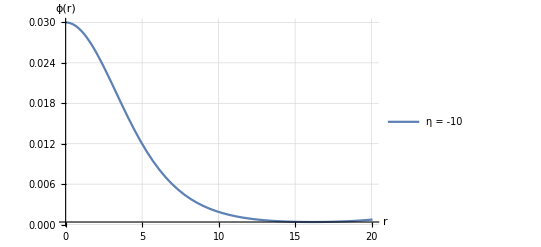

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,20.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6};

α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=SetPrecision[Bs[[2]],prec];
rMax=SetPrecision[Bs[[3]],prec];
rMin=10^-5;

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

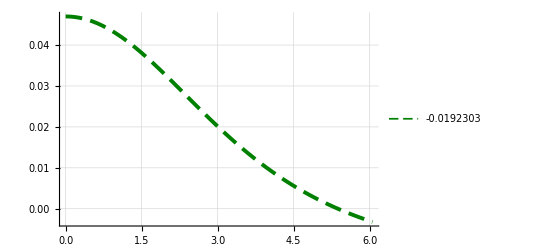

```mathematica
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rTest},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s](*AA[[1]]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

```mathematica
w
```

```mathematica
ϕ0
```

```mathematica
Dat03={{0.00092000000000000002782496455466798579436726868152618408203125`60.,1.0030117187500000026749435999562365395831875503063201904296875`60.,100.061,60,0.3,0.001`60.},{0.00129600000000000027677860003905152552761137485504150390625`60.,1.0042504882812500037751919645945264392139506526291370391845703125`60.,100.061,60,0.3,0.001`60.},{0.00167200000000000009205136652923329165787436068058013916015625`60.,1.00549487304687500488042765922624965924114803783595561981201171875`60.,100.061,60,0.3,0.001`60.},{0.002048000000000000341005002013616831391118466854095458984375`60.,1.00674447631835938099029831814534841072372728376649320125579833984375`60.,100.061,60,0.3,0.001`60.},{0.0024240000000000003731182030008994843228720128536224365234375`60.,1.0079994125366211008549055853054932097023765891208313405513763427734375`60.,100.061,60,0.3,0.001`60.},{0.0027999999999999999715505349939803636516444385051727294921875`60.,1.009259292602539070723903871264204301638756078318692743778228759765625`60.,100.061,60,0.3,0.001`60.},{0.003000000000000000062450045135165055398829281330108642578125`60.,1.009931670814752477670806756146764000814375350500995409674942493438720703125`60.,100.061,60,0.3,0.001`60.},{0.004166666666666666608842550800773096852935850620269775390625`60.,1.01388324472709782461432445997887803833920842416782548411902098450809717178345`60.,100.061,60,0.3,0.001`60.},{0.00533333333333333402259679445478468551300466060638427734375`60.,1.01788602066795275033336755225289954312819780228582811076876168954186141490936`60.,100.061,60,0.3,0.001`60.},{0.00650000000000000056898930012039272696711122989654541015625`60.,1.02194063729381160029795514188004001125168245788383527758447222311133373295888`60.,100.061,60,0.3,0.001`60.},{0.007000000000000000145716771982051795930601656436920166015625`60.,1.02369439299207526417401115141510307340503558887635088270329219994891900569201`60.,90.061,60,0.3,0.001`60.},{0.007749999999999999944488848768742172978818416595458984375`60.,1.02634324454998982393617150075814923128772098669646024166057785009797953534871`60.,90.061,60,0.3,0.001`60.},{0.008500000000000000610622663543836097232997417449951171875`60.,1.02901387154300783378020630185814328332395700383000269190203468383515428286046`60.,90.061,60,0.3,0.001`60.},{0.00899999999999999931998839741709161899052560329437255859375`60.,1.03080690575145212030023477718957801031525246305848436678687107814766932278872`60.,80.061,60,0.3,0.001`60.},{0.01000000000000000020816681711721685132943093776702880859375`60.,1.03442297826519638479028247459752466183848201679296163746357706259004771709442`60.,70.061,60,0.3,0.001`60.},{0.0125000000000000006938893903907228377647697925567626953125`60.,1.04364089435356433297434048379530679776774817341111756263671850319951772689819`60.,70.061,60,0.3,0.001`60.},{0.01299999999999999940325512426397835952229797840118408203125`60.,1.0455154752731322981721141774334726814998930422007106244564056396484375`60.,40.061,60,0.3,0.001`60.},{0.01400000000000000029143354396410359186120331287384033203125`60.,1.04929629802703851565280832578742897798207422965788282454013824462890625`60.,40.061,60,0.3,0.001`60.},{0.01499999999999999944488848768742172978818416595458984375`60.,1.05311948966979974981253149850235484308313971268944442272186279296875`60.,40.061,60,0.3,0.001`60.},{0.0179999999999999986399767948341832379810512065887451171875`60.,1.06485062134265897115191216974077782764229738177164108492434024810791015625`60.,40.0601,60,0.3,0.0001`60.},{0.0200000000000000004163336342344337026588618755340576171875`60.,1.072894287109375044292369251464069890289465547539293766021728515625`60.,25.060100000000002,60,0.3,0.0001`60.},{0.022499999999999999167332731531132594682276248931884765625`60.,1.0832080078125000370948931294190487051309901289641857147216796875`60.,25.060100000000002,60,0.3,0.0001`60.},{0.025000000000000001387778780781445675529539585113525390625`60.,1.09381439208984377969318042313207062221636078902520239353179931640625`60.,25.060100000000002,60,0.3,0.0001`60.},{0.0259999999999999988065102485279567190445959568023681640625`60.,1.09816406250000007070732888081465716823004186153411865234375`60.,18.060010000000002,60,0.3,1.`60.*^-5},{0.0279999999999999971134201359745929948985576629638671875`60.,1.106972656250000060750016128707784446305595338344573974609375`60.,18.060010000000002,60,0.3,1.`60.*^-5},{0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5},{0.0350000000000000033306690738754696212708950042724609375`60.,1.13940429687499998091804176425512196146883070468902587890625`60.,18.06001,60,0.3,1.`60.*^-5},{0.0400000000000000077715611723760957829654216766357421875`60.,1.164275512695312470522711334464105448205373249948024749755859375`60.,18.060010000000002,60,0.3,1.`60.*^-5},{0.04499999999999999833466546306226518936455249786376953125`60.,1.19057812499999994722277296688162095961160957813262939453125`60.,15.06001,60,0.3,1.`60.*^-5},{0.05000000000000000277555756156289135105907917022705078125`60.,1.2186083984374999418694163200171942662564106285572052001953125`60.,15.06001,60,0.3,1.`60.*^-5},{0.051999999999999997613020497055913438089191913604736328125`30.,1.2298499999999999154898233655330841429531574249267578125`30.,10.060001,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.053999999999999999389377336456163902767002582550048828125`30.,1.24278749999999994779731338212513946928083896636962890625`30.,10.060001,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.056,1.2545,15,60,0.3,10^-6},{0.06,1.28018,12,30,0.3,10^-6}};
```

```mathematica
Datm03={{0.0008999999999999999753669266411293392593506723642349243164`30.,1.002941894531250056490998944641601653415818873327225446701`30.,90.061,30,-0.3,10^-3},{0.00092000000000000002782496455466798579436726868152618408203125`60.,1.003011718749999986628751447170770916272886097431182861328125`60.,100.061,60,-0.3,0.001`60.},{0.00129600000000000027677860003905152552761137485504150390625`60.,1.004250305175781218084449068761454526566012646071612834930419921875`60.,100.061,60,-0.3,0.001`60.},{0.00167200000000000009205136652923329165787436068058013916015625`60.,1.0054948730468749494505915909048354706101235933601856231689453125`60.,100.061,60,-0.3,0.001`60.},{0.002048000000000000341005002013616831391118466854095458984375`60.,1.006744514465331961990772198338450760246587378787808120250701904296875`60.,100.061,60,-0.3,0.001`60.},{0.0024240000000000003731182030008994843228720128536224365234375`60.,1.007999476432800204920042745214588120195031706316513009369373321533203125`60.,100.061,60,-0.3,0.001`60.},{0.0029100000000000002600697435184429195942357182502746582031`30.,1.0096290707588196387964010499137246495288122716260659217369`30.,90.061,30,-0.3,10^-3},{0.004920000000000000761612994892857386730611324310302734375`30.,1.0164625474950299276896850658824078646138742380161668066307`30.,90.061,30,-0.3,10^-3},{0.0069300000000000003957945082788683066610246896743774414062`30.,1.0234498030065879626115298317316712883946142239861929607025`30.,92.061,30,-0.3,10^-3},{0.0089400000000000017646994976416863210033625364303588867188`30.,1.030594532029044851005172410378025284137253304694696338234`30.,93.061,30,-0.3,10^-3},{0.0091000000000000004496403249731883988715708255767822265625`30.,1.0311701387532537614333723330074617653904393108735608691837`30.,90.061,30,-0.3,10^-3},{0.0092999999999999992394972281317677698098123073577880859375`30.,1.0318912281160010686235844299399885794567479507539281557982`30.,76.061,30,-0.3,10^-3},{0.0094999999999999997640776072671542351599782705307006835938`30.,1.0326138473246829316655783752630477362878949832347350024087`30.,75.061,30,-0.3,10^-3},{0.0118000000000000014599432773820808506570756435394287109375`30.,1.041041833898771098790348077080324265937301901488320126346`30.,75.061,30,-0.3,10^-3},{0.0140000000000000002914335439641035918612033128738403320312`30.,1.0493096643520403441406366802502799349343783698361790013287`30.,60.061,30,-0.3,10^-3},{0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3},{0.0167999999999999989619414719754786347039043903350830078125`50.,1.060134887695312553410509522067162180292143602855503559112548828125`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.01764000000000000289990254032090888358652591705322265625`50.,1.063449096679687556354118420365306718622377957217395305633544921875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.0184799999999999998989697047591107548214495182037353515625`50.,1.06679687500000005932754287840680262888781726360321044921875`50.,30.060100000000173,50,-0.3,0.0001`50.},{0.0193200000000000003674838211509268148802220821380615234375`50.,1.070175170898437562328072390760436150003442890010774135589599609375`50.,30.06010000000006,50,-0.3,0.0001`50.},{0.0201600000000000008359979375427428749389946460723876953125`50.,1.073587036132812565358417462857421043054273468442261219024658203125`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0210000000000000013045120539345589349977672100067138671875`50.,1.07703170776367194341790046833995386776905434089712798595428466796875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.021999999999999998723243521681069978512823581695556640625`50.,1.0811759948730469009490237457249417474258734728209674358367919921875`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0350000000000000033306690738754696212708950042724609375`50.,1.1396667480468749913155405983911094836003030650317668914794921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.040000000000000000832667268468867405317723751068115234375`50.,1.16466979980468747651075993310154643722853506915271282196044921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.04499999999999999833466546306226518936455249786376953125`50.,1.1910937499999999476807399645394980325363576412200927734375`50.,14.060001,50,-0.3,1.`50.*^-6},{0.05000000000000000277555756156289135105907917022705078125`60.,1.21992187499999997328525846995717074605636298656463623046875`60.,11.060001,60,-0.3,1.`60.*^-6},{0.059999999999999997779553950749686919152736663818359375`60.,1.280937500000000027478019859472624375484883785247802734375`60.,11.060001,60,-0.3,1.`60.*^-6},{0.061999999999999999555910790149937383830547332763671875`60.,1.2962500000000000410782519111307919956743717193603515625`60.,9.060001,60,-0.3,1.`60.*^-6},{0.064000000000000001332267629550187848508358001708984375`60.,1.314062500000000056898930012039272696711122989654541015625`60.,8.060001,60,-0.3,1.`60.*^-6}};
```

### Shooting

```mathematica
L1=1; η=-0.3;ϕ0=0.015; α=1;
k=1/16/ π;mS=1;rMin=10^-3; rMax=50;
ϕFlat=0;
r0=1;
rGoal = rMax+2; 
(* start interval for search of omega, fixed by hand *)
omUP=1.6352038952049000;(* 1.539405047009914752*)
omLOW=1.057169212308494000;(*1.532277585403724000 *)

(* switch off some error messages *)
Off[NDSolve::ndsz];
 Off[NDSolve::icfail]; 
Off[InterpolatingFunction::dmval];

While[ϕFlat==0,
(*
Print["Memory Occupied: ", MemoryInUse[]];
*)
(* Controlando memoria y precision en la frecuencia *)
Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];Break[],
(omUP-omLOW)/2<10^-15, (* Fijando la maxima precision en w a 10^-15 *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];Break[]
           ];
(* *)
(*
Print["omLOW = ", NumberForm[omLOW,{18,19}]];
Print["omUP  = ", NumberForm[omUP,{18,19}]];
Print["Δω = ",NumberForm[(omUP-omLOW)/2,{18,19}]];
*)
w=(omLOW+omUP)/2;
(*w=RandomReal[{omLOW,omUP},WorkingPrecision->18];*)

(*
Print["ω = ",NumberForm[w,{19,18}]," r = ",rTest];
Print["\n"];
*)
s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

(* shotting *)
For[rTest =r0, rTest <rGoal,rTest+=0.001,
       (*   Print[ "rTest = ", rTest, "   ϕ[rTest] = ", Evaluate[φ[rTest]/.s][[1]] ];*)
Which[Re[Evaluate[φ[rTest]/.s][[1]]]<10^-9,
(*Print[" --> Problem with boundary conditions change"];*)
omLOW=omLOW+1.97*10^-6;
Break[],
Re[Evaluate[φ[rTest]/.s][[1]]]>10^3,
(*Print[" --> Problem with boundary conditions change"];*)
omLOW=omLOW+1325*10^6;
Break[],
Re[Evaluate[φ[rTest]/.s][[1]]]<0,
Print["rTest = ", rTest, " --> ϕ negative --> decreasing Upper Bound of omega"];
Print["ω = ",NumberForm[w,{19,18}]," r = ",rTest];
omUP=w;
(*Print["eqϕ ",SeidelEqsList[[1,1]]];
ϕFlat=1;*)
Break[],
Re[Evaluate[φ[rTest+rTest/2]/.s][[1]]]>Re[Evaluate[φ[rTest]/.s][[1]]]&&rTest>rMin,
Print["rTest = ", rTest, " -> ϕ Local Minimum -> increasing Lower Bound of omega"];
Print["ω = ",NumberForm[w,{19,18}]," r = ",rTest];
omLOW=w;
(*Print["eqϕ ",SeidelEqsList[[1,1]]];
ϕFlat=1;*)
Break[],
rTest> rGoal-1,
Print["rTest = ", rTest, " --> rGoal reached"];
ϕFlat=1;
Break[],
Evaluate[φ[rTest]/.s][[1]]==1,
(*Print[" --> Problem with boundary conditions"];*)
omLOW=omLOW+1*10^-5;
Break[]
          ](*Which*)   
     ](* FOR *)
 ](* While *)
(* Resultados *)
Speak["o mega is calculated"]

Print["ω = ",NumberForm[w,{19,18}]];
Print["Δω = ",NumberForm[(omUP-omLOW)/2,{19,18}]];

(* Plot the scalar field *)
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rTest},
Background->White,PlotLegends->{"ϕ"},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::nderr: Error test failure at r == 8.63654; unable to continue.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::nderr: Error test failure at r == 11.7127; unable to continue.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

General::stop: Further output of NDSolve::ivres will be suppressed during this calculation.

NDSolve::nderr: Error test failure at r == 11.7128; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at r == 11.692; unable to continue.

```mathematica
etam01={{0.001,1.003276824951172000,90},{0.002,1.006584667964717000,100},{0.003,1.009931740264392000,100},{0.005,1.016737498965354000,72},{0.01,"1.034426108133757000",100},{0.015,"1.053130578785699000",56},{0.02,1.072920024263826709,55},{0.03,,36},{0.04,,24},{0.042,,17},{0.044, ,14},{0.048,,12},{0.05,,16},{0.052,,13},{0.054,,16},{0.056,,16},{0.058,,11},{0.06,,16},{0.07,,16},{0.08,,11},{0.09,,13},{0.1,,12},{0.11, ,11},{0.13, ,16}};
```

### Grap. data

```mathematica
etam01={{0.001,1.003276824951172000,90},{0.002,1.006584667964717000,100},{0.003,1.009931740264392000,100},{0.005,1.016737498965354000,72},{0.01,"1.034426108133757000",100},{0.015,"1.053130578785699000",56},{0.02,1.072920024263826709,55}};
```

```mathematica
{{0.056,1.2545,15,60,0.3,10^-6}};
```

```mathematica
{{0.0000100000000000000008180305391403130954586231382563710213`30.,1.00007812500000004164854225385816732796229189261794090271`30.,250.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0000900000000000000056682089577542171809909632429480552673`30.,1.0002929687500000416902840374988592486715788254514336585999`30.,250.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6}};
```

```mathematica
Dat=%;
```

Plot the profile of phi

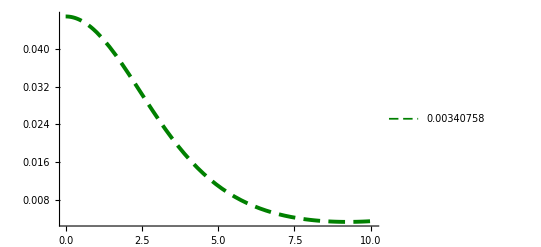

```mathematica
Table[
AA=Dat[[i]];
prec=AA[[4]];
η= AA[[5]]; 
α=1;k=1/16/ π;mS=1;
rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec];
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];

(*s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];*)

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; 

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s](*AA[[1]]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
AxesOrigin->{0,0}],{i,1,Length[Dat]}]
```

### Test

```mathematica
etam01={{0.001,1.003276824951172000,90},{0.002,1.006584667964717000,100},{0.003,1.009931740264392000,100},{0.005,1.016737498965354000,72},{0.01,"1.034426108133757000",100},{0.015,"1.053130578785699000",56},{0.02,1.072920024263826709,55}};
```

```mathematica
{0.056,1.28018,12,60,0.3,10^-6}
```

```mathematica
1.2808
```

```mathematica
L1=1; η=0.3;ϕ0=0.06; α=1;
k=1/16/ π;mS=1;rMin=10^-6; w=1.28018;rMax=12;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

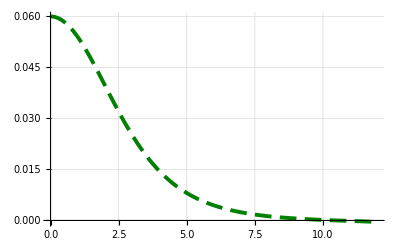

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,rMax},
Background->White,
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic,AxesOrigin->{0,0}]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

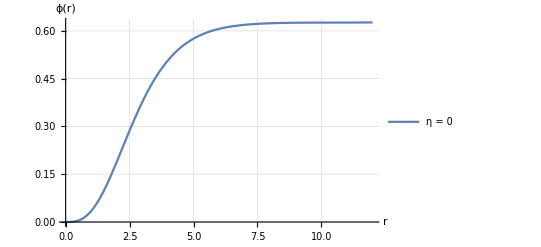

```mathematica
Plot[{Evaluate[M[r]/.s1]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

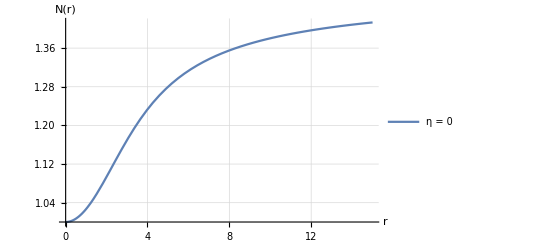

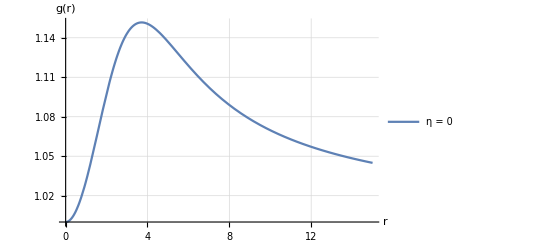

```mathematica
(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.s1]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.56}],
PlotRange->Full,AxesLabel->{"r","N(r)"},
GridLines->Automatic]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"η = 0"(*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.7}],PlotRange->Full,
AxesLabel->{"r","g(r)"},
GridLines->Automatic]
```

## Data

```mathematica
Dat03={(*{0.0000100000000000000008180305391403130954586231382563710213`30.,1.00007812500000004164854225385816732796229189261794090271`30.,250.060001,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0000900000000000000056682089577542171809909632429480552673`30.,1.0002929687500000416902840374988592486715788254514336585999`30.,250.060001,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},*){0.00092000000000000002782496455466798579436726868152618408203125`60.,1.0030117187500000026749435999562365395831875503063201904296875`60.,100.061,60,0.3,0.001`60.},{0.00129600000000000027677860003905152552761137485504150390625`60.,1.0042504882812500037751919645945264392139506526291370391845703125`60.,100.061,60,0.3,0.001`60.},{0.00167200000000000009205136652923329165787436068058013916015625`60.,1.00549487304687500488042765922624965924114803783595561981201171875`60.,100.061,60,0.3,0.001`60.},{0.002048000000000000341005002013616831391118466854095458984375`60.,1.00674447631835938099029831814534841072372728376649320125579833984375`60.,100.061,60,0.3,0.001`60.},{0.0024240000000000003731182030008994843228720128536224365234375`60.,1.0079994125366211008549055853054932097023765891208313405513763427734375`60.,100.061,60,0.3,0.001`60.},{0.0027999999999999999715505349939803636516444385051727294921875`60.,1.009259292602539070723903871264204301638756078318692743778228759765625`60.,100.061,60,0.3,0.001`60.},{0.003000000000000000062450045135165055398829281330108642578125`60.,1.009931670814752477670806756146764000814375350500995409674942493438720703125`60.,100.061,60,0.3,0.001`60.},{0.004166666666666666608842550800773096852935850620269775390625`60.,1.01388324472709782461432445997887803833920842416782548411902098450809717178345`60.,100.061,60,0.3,0.001`60.},{0.00533333333333333402259679445478468551300466060638427734375`60.,1.01788602066795275033336755225289954312819780228582811076876168954186141490936`60.,100.061,60,0.3,0.001`60.},{0.00650000000000000056898930012039272696711122989654541015625`60.,1.02194063729381160029795514188004001125168245788383527758447222311133373295888`60.,100.061,60,0.3,0.001`60.},{0.007000000000000000145716771982051795930601656436920166015625`60.,1.02369439299207526417401115141510307340503558887635088270329219994891900569201`60.,90.061,60,0.3,0.001`60.},{0.007749999999999999944488848768742172978818416595458984375`60.,1.02634324454998982393617150075814923128772098669646024166057785009797953534871`60.,90.061,60,0.3,0.001`60.},{0.008500000000000000610622663543836097232997417449951171875`60.,1.02901387154300783378020630185814328332395700383000269190203468383515428286046`60.,90.061,60,0.3,0.001`60.},{0.00899999999999999931998839741709161899052560329437255859375`60.,1.03080690575145212030023477718957801031525246305848436678687107814766932278872`60.,80.061,60,0.3,0.001`60.},{0.01000000000000000020816681711721685132943093776702880859375`60.,1.03442297826519638479028247459752466183848201679296163746357706259004771709442`60.,70.061,60,0.3,0.001`60.},{0.0125000000000000006938893903907228377647697925567626953125`60.,1.04364089435356433297434048379530679776774817341111756263671850319951772689819`60.,70.061,60,0.3,0.001`60.},{0.01299999999999999940325512426397835952229797840118408203125`60.,1.0455154752731322981721141774334726814998930422007106244564056396484375`60.,40.061,60,0.3,0.001`60.},{0.01400000000000000029143354396410359186120331287384033203125`60.,1.04929629802703851565280832578742897798207422965788282454013824462890625`60.,40.061,60,0.3,0.001`60.},{0.01499999999999999944488848768742172978818416595458984375`60.,1.05311948966979974981253149850235484308313971268944442272186279296875`60.,40.061,60,0.3,0.001`60.},{0.0179999999999999986399767948341832379810512065887451171875`60.,1.06485062134265897115191216974077782764229738177164108492434024810791015625`60.,40.0601,60,0.3,0.0001`60.},{0.0200000000000000004163336342344337026588618755340576171875`60.,1.072894287109375044292369251464069890289465547539293766021728515625`60.,25.060100000000002,60,0.3,0.0001`60.},{0.022499999999999999167332731531132594682276248931884765625`60.,1.0832080078125000370948931294190487051309901289641857147216796875`60.,25.060100000000002,60,0.3,0.0001`60.},{0.025000000000000001387778780781445675529539585113525390625`60.,1.09381439208984377969318042313207062221636078902520239353179931640625`60.,25.060100000000002,60,0.3,0.0001`60.},{0.0259999999999999988065102485279567190445959568023681640625`60.,1.09816406250000007070732888081465716823004186153411865234375`60.,18.060010000000002,60,0.3,1.`60.*^-5},{0.0279999999999999971134201359745929948985576629638671875`60.,1.106972656250000060750016128707784446305595338344573974609375`60.,18.060010000000002,60,0.3,1.`60.*^-5},{0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5},{0.0350000000000000033306690738754696212708950042724609375`60.,1.13940429687499998091804176425512196146883070468902587890625`60.,18.06001,60,0.3,1.`60.*^-5},{0.0400000000000000077715611723760957829654216766357421875`60.,1.164275512695312470522711334464105448205373249948024749755859375`60.,18.060010000000002,60,0.3,1.`60.*^-5},{0.04499999999999999833466546306226518936455249786376953125`60.,1.19057812499999994722277296688162095961160957813262939453125`60.,15.06001,60,0.3,1.`60.*^-5},{0.05000000000000000277555756156289135105907917022705078125`60.,1.2186083984374999418694163200171942662564106285572052001953125`60.,15.06001,60,0.3,1.`60.*^-5},(*{0.051999999999999997613020497055913438089191913604736328125`30.,1.2298499999999999154898233655330841429531574249267578125`30.,10.060001,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.053999999999999999389377336456163902767002582550048828125`30.,1.24278749999999994779731338212513946928083896636962890625`30.,10.060001,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},*){0.056,1.2545,15,60,0.3,10^-6},{0.06,1.28018,12,30,0.3,10^-6}};
```

```mathematica
Datm03={{0.0000100000000000000008180305391403130954586231382563710213`30.,1.00007812500000004164854225385816732796229189261794090271`30.,250.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0000900000000000000056682089577542171809909632429480552673`30.,1.0002929687500000416902840374988592486715788254514336585999`30.,250.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0008999999999999999753669266411293392593506723642349243164`30.,1.002941894531250056490998944641601653415818873327225446701`30.,90.061,30,-0.3,10^-3},{0.00092000000000000002782496455466798579436726868152618408203125`60.,1.003011718749999986628751447170770916272886097431182861328125`60.,100.061,60,-0.3,0.001`60.},{0.00129600000000000027677860003905152552761137485504150390625`60.,1.004250305175781218084449068761454526566012646071612834930419921875`60.,100.061,60,-0.3,0.001`60.},{0.00167200000000000009205136652923329165787436068058013916015625`60.,1.0054948730468749494505915909048354706101235933601856231689453125`60.,100.061,60,-0.3,0.001`60.},{0.002048000000000000341005002013616831391118466854095458984375`60.,1.006744514465331961990772198338450760246587378787808120250701904296875`60.,100.061,60,-0.3,0.001`60.},{0.0024240000000000003731182030008994843228720128536224365234375`60.,1.007999476432800204920042745214588120195031706316513009369373321533203125`60.,100.061,60,-0.3,0.001`60.},{0.0029100000000000002600697435184429195942357182502746582031`30.,1.0096290707588196387964010499137246495288122716260659217369`30.,90.061,30,-0.3,10^-3},{0.004920000000000000761612994892857386730611324310302734375`30.,1.0164625474950299276896850658824078646138742380161668066307`30.,90.061,30,-0.3,10^-3},{0.0069300000000000003957945082788683066610246896743774414062`30.,1.0234498030065879626115298317316712883946142239861929607025`30.,92.061,30,-0.3,10^-3},{0.0070000000000000001457167719820517959306016564369201660156`30.,1.023695957845322954578643242728211661707178498762413306244`30.,92.061,30,-0.3,0.001`30.},{0.0089400000000000017646994976416863210033625364303588867188`30.,1.030594532029044851005172410378025284137253304694696338234`30.,93.061,30,-0.3,10^-3},{0.0091000000000000004496403249731883988715708255767822265625`30.,1.0311701387532537614333723330074617653904393108735608691837`30.,90.061,30,-0.3,10^-3},{0.0092999999999999992394972281317677698098123073577880859375`30.,1.0318912281160010686235844299399885794567479507539281557982`30.,76.061,30,-0.3,10^-3},{0.0094999999999999997640776072671542351599782705307006835938`30.,1.0326138473246829316655783752630477362878949832347350024087`30.,75.061,30,-0.3,10^-3},{0.0118000000000000014599432773820808506570756435394287109375`30.,1.041041833898771098790348077080324265937301901488320126346`30.,75.061,30,-0.3,10^-3},{0.0140000000000000002914335439641035918612033128738403320312`30.,1.0493096643520403441406366802502799349343783698361790013287`30.,60.061,30,-0.3,10^-3},{0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3},{0.0167999999999999989619414719754786347039043903350830078125`50.,1.060134887695312553410509522067162180292143602855503559112548828125`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.01764000000000000289990254032090888358652591705322265625`50.,1.063449096679687556354118420365306718622377957217395305633544921875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.0184799999999999998989697047591107548214495182037353515625`50.,1.06679687500000005932754287840680262888781726360321044921875`50.,30.060100000000173,50,-0.3,0.0001`50.},{0.0193200000000000003674838211509268148802220821380615234375`50.,1.070175170898437562328072390760436150003442890010774135589599609375`50.,30.06010000000006,50,-0.3,0.0001`50.},{0.0201600000000000008359979375427428749389946460723876953125`50.,1.073587036132812565358417462857421043054273468442261219024658203125`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0210000000000000013045120539345589349977672100067138671875`50.,1.07703170776367194341790046833995386776905434089712798595428466796875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.021999999999999998723243521681069978512823581695556640625`50.,1.0811759948730469009490237457249417474258734728209674358367919921875`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0350000000000000033306690738754696212708950042724609375`50.,1.1396667480468749913155405983911094836003030650317668914794921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.040000000000000000832667268468867405317723751068115234375`50.,1.16466979980468747651075993310154643722853506915271282196044921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.04499999999999999833466546306226518936455249786376953125`50.,1.1910937499999999476807399645394980325363576412200927734375`50.,14.060001,50,-0.3,1.`50.*^-6},{0.05000000000000000277555756156289135105907917022705078125`60.,1.21992187499999997328525846995717074605636298656463623046875`60.,11.060001,60,-0.3,1.`60.*^-6},{0.059999999999999997779553950749686919152736663818359375`60.,1.280937500000000027478019859472624375484883785247802734375`60.,11.060001,60,-0.3,1.`60.*^-6},{0.061999999999999999555910790149937383830547332763671875`60.,1.2962500000000000410782519111307919956743717193603515625`60.,9.060001,60,-0.3,1.`60.*^-6},{0.064000000000000001332267629550187848508358001708984375`60.,1.314062500000000056898930012039272696711122989654541015625`60.,8.060001,60,-0.3,1.`60.*^-6}};
```

## Compact

```mathematica
Datm03={{0.0008999999999999999753669266411293392593506723642349243164`30.,1.002941894531250056490998944641601653415818873327225446701`30.,90.061,30,-0.3,10^-3},{0.00092000000000000002782496455466798579436726868152618408203125`60.,1.003011718749999986628751447170770916272886097431182861328125`60.,100.061,60,-0.3,0.001`60.},{0.00129600000000000027677860003905152552761137485504150390625`60.,1.004250305175781218084449068761454526566012646071612834930419921875`60.,100.061,60,-0.3,0.001`60.},{0.00167200000000000009205136652923329165787436068058013916015625`60.,1.0054948730468749494505915909048354706101235933601856231689453125`60.,100.061,60,-0.3,0.001`60.},{0.002048000000000000341005002013616831391118466854095458984375`60.,1.006744514465331961990772198338450760246587378787808120250701904296875`60.,100.061,60,-0.3,0.001`60.},{0.0024240000000000003731182030008994843228720128536224365234375`60.,1.007999476432800204920042745214588120195031706316513009369373321533203125`60.,100.061,60,-0.3,0.001`60.},{0.0029100000000000002600697435184429195942357182502746582031`30.,1.0096290707588196387964010499137246495288122716260659217369`30.,90.061,30,-0.3,10^-3},{0.004920000000000000761612994892857386730611324310302734375`30.,1.0164625474950299276896850658824078646138742380161668066307`30.,90.061,30,-0.3,10^-3},{0.0069300000000000003957945082788683066610246896743774414062`30.,1.0234498030065879626115298317316712883946142239861929607025`30.,92.061,30,-0.3,10^-3},{0.0089400000000000017646994976416863210033625364303588867188`30.,1.030594532029044851005172410378025284137253304694696338234`30.,93.061,30,-0.3,10^-3},{0.0091000000000000004496403249731883988715708255767822265625`30.,1.0311701387532537614333723330074617653904393108735608691837`30.,90.061,30,-0.3,10^-3},{0.0092999999999999992394972281317677698098123073577880859375`30.,1.0318912281160010686235844299399885794567479507539281557982`30.,76.061,30,-0.3,10^-3},{0.0094999999999999997640776072671542351599782705307006835938`30.,1.0326138473246829316655783752630477362878949832347350024087`30.,75.061,30,-0.3,10^-3},{0.0118000000000000014599432773820808506570756435394287109375`30.,1.041041833898771098790348077080324265937301901488320126346`30.,75.061,30,-0.3,10^-3},{0.0140000000000000002914335439641035918612033128738403320312`30.,1.0493096643520403441406366802502799349343783698361790013287`30.,60.061,30,-0.3,10^-3},{0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3},{0.0167999999999999989619414719754786347039043903350830078125`50.,1.060134887695312553410509522067162180292143602855503559112548828125`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.01764000000000000289990254032090888358652591705322265625`50.,1.063449096679687556354118420365306718622377957217395305633544921875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.0184799999999999998989697047591107548214495182037353515625`50.,1.06679687500000005932754287840680262888781726360321044921875`50.,30.060100000000173,50,-0.3,0.0001`50.},{0.0193200000000000003674838211509268148802220821380615234375`50.,1.070175170898437562328072390760436150003442890010774135589599609375`50.,30.06010000000006,50,-0.3,0.0001`50.},{0.0201600000000000008359979375427428749389946460723876953125`50.,1.073587036132812565358417462857421043054273468442261219024658203125`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0210000000000000013045120539345589349977672100067138671875`50.,1.07703170776367194341790046833995386776905434089712798595428466796875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.021999999999999998723243521681069978512823581695556640625`50.,1.0811759948730469009490237457249417474258734728209674358367919921875`50.,30.060100000000073,50,-0.3,0.0001`50.},

{0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,18,30,-0.3,10^-5},

{0.0350000000000000033306690738754696212708950042724609375`50.,1.1396667480468749913155405983911094836003030650317668914794921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.040000000000000000832667268468867405317723751068115234375`50.,1.16466979980468747651075993310154643722853506915271282196044921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.04499999999999999833466546306226518936455249786376953125`50.,1.1910937499999999476807399645394980325363576412200927734375`50.,14.060001,50,-0.3,1.`50.*^-6},
(*
{0.05000000000000000277555756156289135105907917022705078125`60.,1.21992187499999997328525846995717074605636298656463623046875`60.,11.060001,60,-0.3,1.`60.*^-6},*)

{0.059999999999999997779553950749686919152736663818359375`60.,1.280937500000000027478019859472624375484883785247802734375`60.,11.060001,60,-0.3,1.`60.*^-6},{0.061999999999999999555910790149937383830547332763671875`60.,1.2962500000000000410782519111307919956743717193603515625`60.,9.060001,60,-0.3,1.`60.*^-6},{0.064000000000000001332267629550187848508358001708984375`60.,1.314062500000000056898930012039272696711122989654541015625`60.,8.060001,60,-0.3,1.`60.*^-6}};
```

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,18,30,-0.3,10^-5};
```

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5};
```

```mathematica
{{0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,18,30,-0.3,10^-5},{0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5}};
```

```mathematica
Dat=%;
```

```mathematica
Bs=Dat;
```

1

0.131404

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.131404 masa 95, 0.131404 comprobando, True

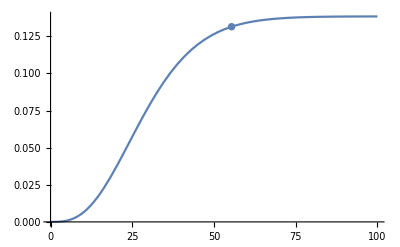

2

0.155748

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.155748 masa 95, 0.155748 comprobando, True

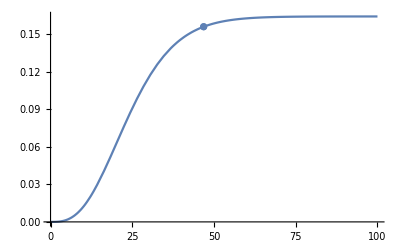

3

0.176252

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.176252 masa 95, 0.176252 comprobando, True

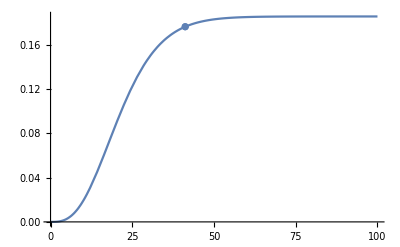

4

0.194321

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.194321 masa 95, 0.194321 comprobando, True

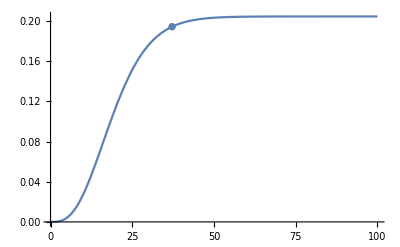

5

0.210592

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.210592 masa 95, 0.210592 comprobando, True

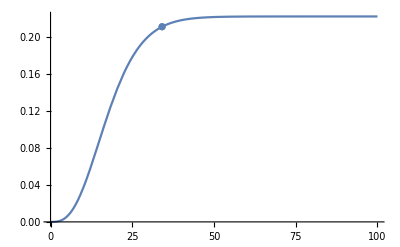

6

0.225457

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.225457 masa 95, 0.225457 comprobando, True

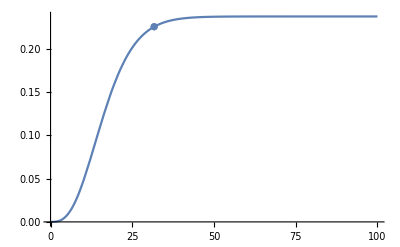

7

0.23289

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.23289 masa 95, 0.23289 comprobando, True

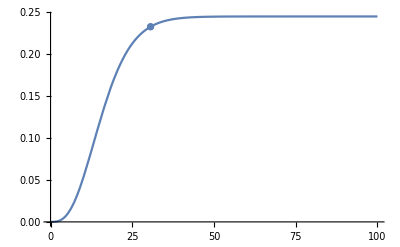

8

0.271173

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.271173 masa 95, 0.271173 comprobando, True

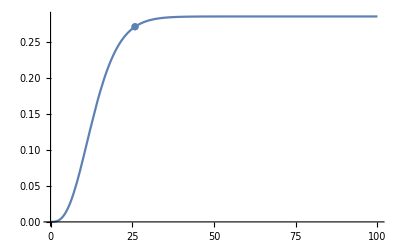

9

0.303134

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.303134 masa 95, 0.303134 comprobando, True

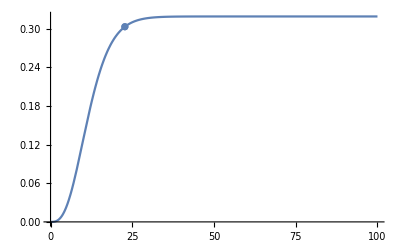

10

0.330667

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.330667 masa 95, 0.330667 comprobando, True

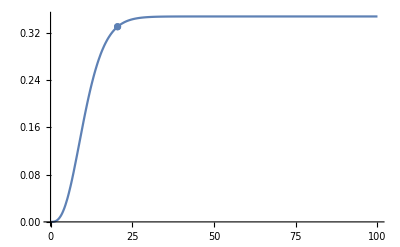

11

0.341389

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.341389 masa 95, 0.341389 comprobando, True

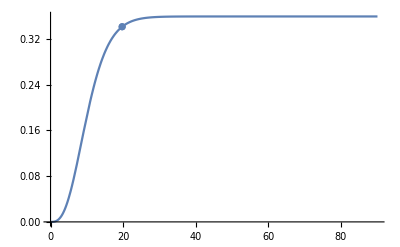

12

0.356469

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.356469 masa 95, 0.356469 comprobando, True

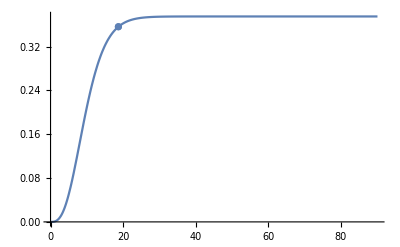

13

0.370476

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.370476 masa 95, 0.370476 comprobando, True

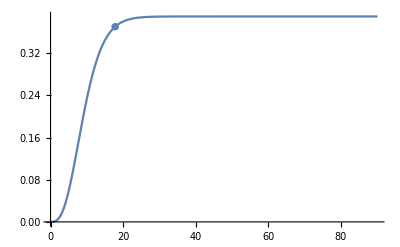

14

0.379275

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.379275 masa 95, 0.379275 comprobando, True

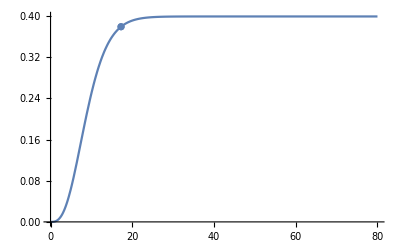

15

0.39574

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.39574 masa 95, 0.39574 comprobando, True

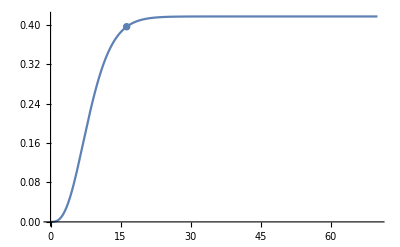

16

0.431382

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.431382 masa 95, 0.431382 comprobando, True

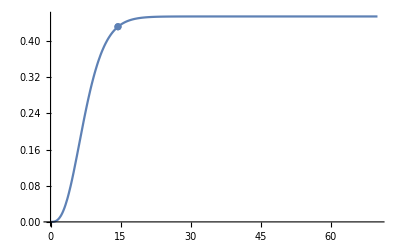

17

0.437712

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.437712 masa 95, 0.437712 comprobando, True

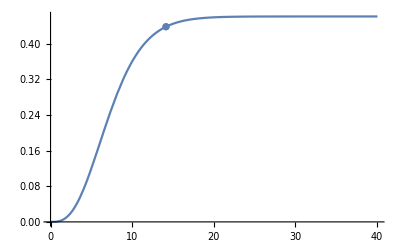

18

0.449671

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.449671 masa 95, 0.449671 comprobando, True

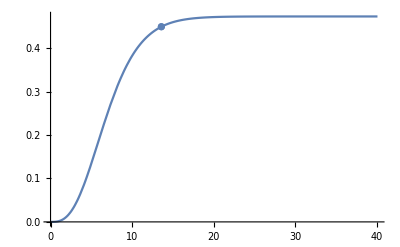

19

0.4608

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.4608 masa 95, 0.4608 comprobando, True

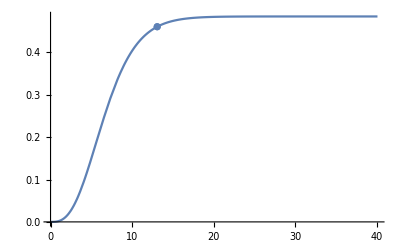

20

0.489848

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.489848 masa 95, 0.489848 comprobando, True

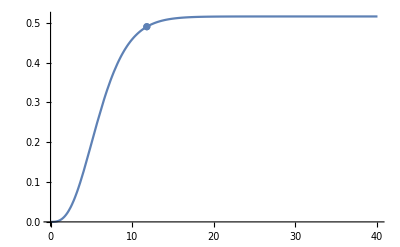

21

0.506099

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.506099 masa 95, 0.506099 comprobando, True

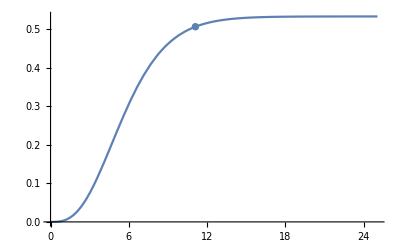

22

0.523595

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.523595 masa 95, 0.523595 comprobando, True

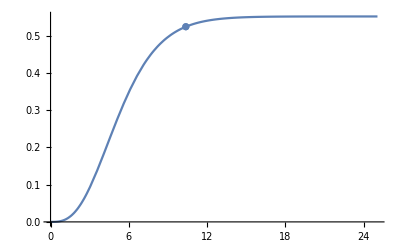

23

0.538681

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.538681 masa 95, 0.538681 comprobando, True

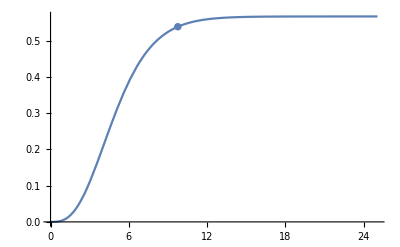

24

0.542827

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.542827 masa 95, 0.542827 comprobando, True

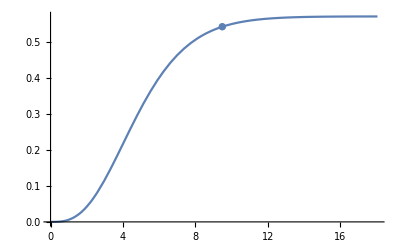

25

0.552452

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.552452 masa 95, 0.552452 comprobando, True

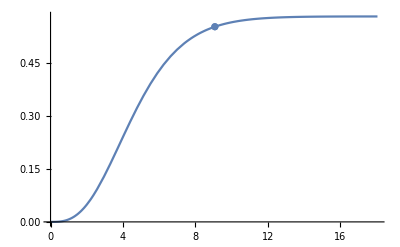

26

0.560421

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.560421 masa 95, 0.560421 comprobando, True

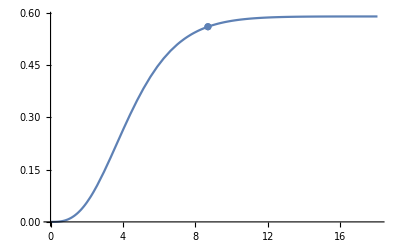

27

0.578944

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.578944 masa 95, 0.578944 comprobando, True

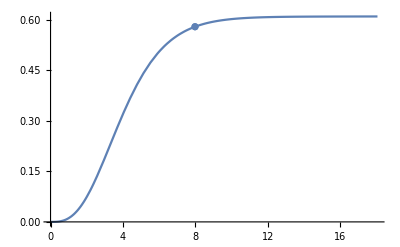

28

0.589398

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.589398 masa 95, 0.589398 comprobando, True

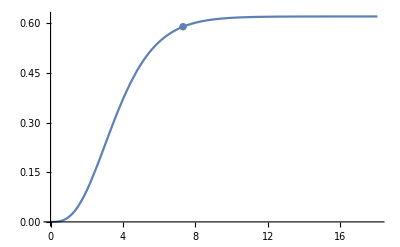

29

0.598089

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.598089 masa 95, 0.598089 comprobando, True

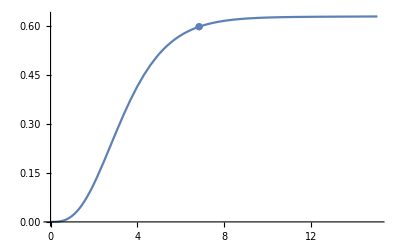

30

0.599641

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.599641 masa 95, 0.599641 comprobando, True

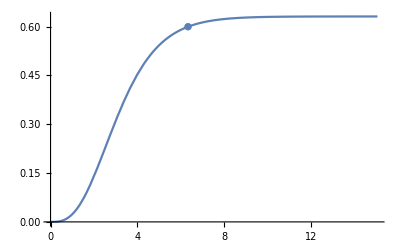

31

0.599722

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.599722 masa 95, 0.599722 comprobando, True

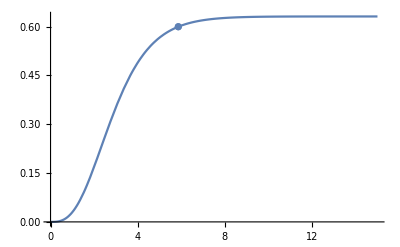

32

0.595141

cumple con ϕ<10^-3

Checking, masa con radio encontrado 0.595141 masa 95, 0.595141 comprobando, True

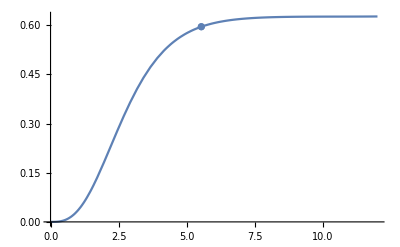

{{55.4011,0.131404},{46.8659,0.155748},{41.2163,0.176252},{37.1938,0.194321},{34.14,0.210592},{31.7171,0.225457},{30.6183,0.23289},{25.8601,0.271173},{22.7524,0.303134},{20.5156,0.330667},{19.7305,0.341389},{18.6963,0.356469},{17.8011,0.370476},{17.2656,0.379275},{16.3164,0.39574},{14.4545,0.431382},{14.1469,0.437712},{13.58,0.449671},{13.0703,0.4608},{11.7979,0.489848},{11.1057,0.506099},{10.371,0.523595},{9.75798,0.538681},{9.48685,0.542827},{9.07813,0.552452},{8.69529,0.560421},{7.9809,0.578944},{7.31963,0.589398},{6.84382,0.598089},{6.33436,0.599641},{5.86216,0.599722},{5.53436,0.595141}}

{{0.996828,0.131404},{0.995529,0.155748},{0.994241,0.176252},{0.992957,0.194321},{0.991678,0.210592},{0.990403,0.225457},{0.989727,0.23289},{0.985806,0.271173},{0.981925,0.303134},{0.978086,0.330667},{0.976453,0.341389},{0.974016,0.356469},{0.971597,0.370476},{0.969993,0.379275},{0.966807,0.39574},{0.958969,0.431382},{0.957423,0.437712},{0.954353,0.449671},{0.951311,0.4608},{0.942354,0.489848},{0.936528,0.506099},{0.929402,0.523595},{0.922419,0.538681},{0.919817,0.542827},{0.914424,0.552452},{0.909196,0.560421},{0.896146,0.578944},{0.884097,0.589398},{0.872322,0.598089},{0.861723,0.599641},{0.849552,0.599722},{0.842631,0.595141}}

{{0.00092000000000000002782496455466798579436726868152618408203125,0.131404},{0.00129600000000000027677860003905152552761137485504150390625,0.155748},{0.00167200000000000009205136652923329165787436068058013916015625,0.176252},{0.002048000000000000341005002013616831391118466854095458984375,0.194321},{0.0024240000000000003731182030008994843228720128536224365234375,0.210592},{0.0027999999999999999715505349939803636516444385051727294921875,0.225457},{0.003000000000000000062450045135165055398829281330108642578125,0.23289},{0.004166666666666666608842550800773096852935850620269775390625,0.271173},{0.00533333333333333402259679445478468551300466060638427734375,0.303134},{0.00650000000000000056898930012039272696711122989654541015625,0.330667},{0.007000000000000000145716771982051795930601656436920166015625,0.341389},{0.007749999999999999944488848768742172978818416595458984375,0.356469},{0.008500000000000000610622663543836097232997417449951171875,0.370476},{0.00899999999999999931998839741709161899052560329437255859375,0.379275},{0.01000000000000000020816681711721685132943093776702880859375,0.39574},{0.0125000000000000006938893903907228377647697925567626953125,0.431382},{0.01299999999999999940325512426397835952229797840118408203125,0.437712},{0.01400000000000000029143354396410359186120331287384033203125,0.449671},{0.01499999999999999944488848768742172978818416595458984375,0.4608},{0.0179999999999999986399767948341832379810512065887451171875,0.489848},{0.0200000000000000004163336342344337026588618755340576171875,0.506099},{0.022499999999999999167332731531132594682276248931884765625,0.523595},{0.025000000000000001387778780781445675529539585113525390625,0.538681},{0.0259999999999999988065102485279567190445959568023681640625,0.542827},{0.0279999999999999971134201359745929948985576629638671875,0.552452},{0.0299999999999999988897769753748434595763683319091796875,0.560421},{0.0350000000000000033306690738754696212708950042724609375,0.578944},{0.0400000000000000077715611723760957829654216766357421875,0.589398},{0.04499999999999999833466546306226518936455249786376953125,0.598089},{0.05000000000000000277555756156289135105907917022705078125,0.599641},{0.056000000000000001165734175856414367444813251495361328125,0.599722},{0.0599999999999999977795539507497,0.595141}}

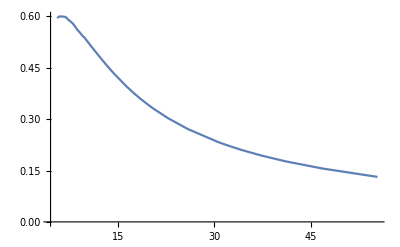

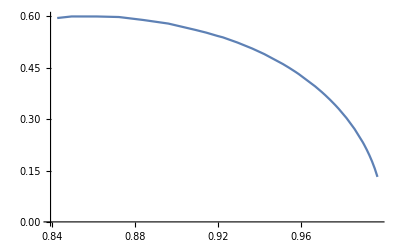

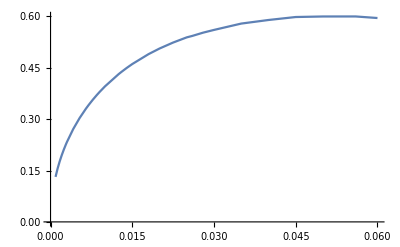

```mathematica
mvsr={};
sphivsswf={};
wfvsm={};
σvsm={};
stop2=0;
α=1;k=1/16/ π;mS=1;L1=1;

For[j=1,j<Length[Bs]+1,j++,
Print[j];
Clear[s,M95, M,rMax,w,η,r0,prec];
r0=1.;
η=Bs[[j,5]];
prec=Bs[[j,4]];
ϕ0=SetPrecision[Bs[[j,1]],prec];
w=SetPrecision[Bs[[j,2]],prec];
rMax=SetPrecision[Bs[[j,3]],prec];
rMin=SetPrecision[Bs[[j,6]],prec];

If[stop2≠0,Break[]]; (*Para cuando una frecuencia no es suficientemente pequeña*)

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]; 

M95=0.95M[rMax][[1]]; (* masa física *)
Print[M95];

(* testeando que el valor de phi en el radio encontrado para la masa 95 sea pequeño *)
If[Evaluate[φ[rMax]/.s][[1]]<5*10^-3,Print["cumple con ϕ<10^-3"],Print["No cumple con ϕ<10^-3"]; Print[ϕ0];Break[]];

rad=Last[FindRoot[M[r]==M95,{r,r0,rMax}]];

Print["Checking, masa con radio encontrado ",  M[rad[[2]]][[1]],  " masa 95, ", M95, " comprobando, ",  M[rad[[2]]][[1]]- M95<10^-4];

(* Frecuencia física, en este caso es raiz, pq uso N, g *)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];

Print[Show[{Plot[M[r],{r,rMin,rMax},AxesOrigin->{0,0}],ListPlot[{{rad[[2]],M95}}]}]];
(* Guardando datos *)
AppendTo[mvsr,{rad[[2]],M95}];
AppendTo[sphivsswf,{w2, M95}];
AppendTo[wfvsm,{ϕ0,M95}];
](* FOR *)
(* Resultados *)
mvsr
sphivsswf
wfvsm

(* Plot*)
(*Show[{ListPlot[mvsr],Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},PlotRange->Full]}]*)
Show[{ListPlot[mvsr,PlotRange->Full,Joined->True]}]
Show[{ListPlot[sphivsswf,PlotRange->Full,Joined->True]}]
Show[{ListPlot[wfvsm,PlotRange->Full,Joined->True]}]
```

```mathematica
A=Interpolation[mvsr,InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
FindMaximum[A[r],{r,4.5,60}]
```

InterpolatingFunction::dmval: Input value {4.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.609814,{r→6.07614}}

InterpolatingFunction::dmval: Input value {4.50113} lies outside the range of data in the interpolating function. Extrapolation will be used.

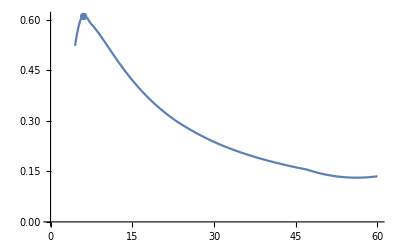

```mathematica
Show[Plot[A[r],{r,4.5,60},AxesOrigin->{0,0}],ListPlot[{{6.076144981101191,0.6098137563767305}}]]
```

```mathematica
rvsM95={};
Do[AppendTo[rvsM95,{r,A[r]}],{r,4.5,60,0.02}]
```

InterpolatingFunction::dmval: Input value {4.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.52} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.54} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

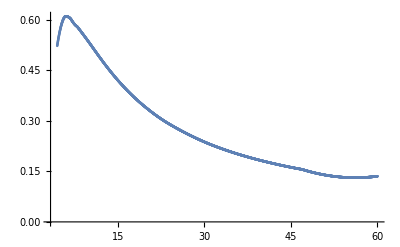

```mathematica
ListPlot[rvsM95,PlotRange->All]
```

```mathematica
Export["Dat_mvsr_etam03.dat",rvsM95]
```

Dat_mvsr_etam03.dat

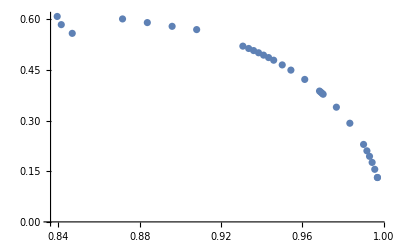

```mathematica
ListPlot[sphivsswf]
```

```mathematica
b=Interpolation[sphivsswf,InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
sphivsswf={{1.0000578397889162,0.00203046360406647},{0.999685727685329,0.04175057758218226},{0.9968586963339668,0.13166524321020734},{0.9968276910121427,0.13140542354669643},{0.9955272915631312,0.15584319341638875},{0.9942407654813953,0.1762624193055023},{0.9929573112163071,0.1943218801502216},{0.9916780638001439,0.21059391291342},{0.990031229095547,0.22958110368393303},{0.9832945754497981,0.29240599825145636},{0.9766785909842111,0.3399551212567568},{0.9701804339259004,0.37829644601527324},{0.9696682115676658,0.3810469184596835},{0.9690291722865497,0.38442300877550617},{0.9683909610077504,0.387754711400692},{0.9611359924467161,0.42220930246969834},{0.954336536356092,0.4498313857595759},{0.9500804565258769,0.4652249474052393},{0.9458794555066712,0.47916639878056244},{0.943377803970755,0.486999851081184},{0.9409102346031455,0.49422027167176646},{0.9384473383744354,0.5012227439506303},{0.9360118421431499,0.5077470603723891},{0.9335938713831874,0.5139388880733806},{0.9307396486844334,0.520884080688577},{0.895991044506921,0.5795848878982532},{0.8838108021169017,0.5906661473799661},(*{0.8716334906612875,0.6014959300486071},*),{0.878,0.6},{0.8683407352574987,0.61207696106588477},{0.86,0.612864},{0.85,0.61},{0.8415442517782166,0.5845718836727563},{0.8469283106668151,0.5587655063987228}};
```

```mathematica
Export["Dat_wvsM95_etam03.dat",sphivsswf]
```

Dat_wvsM95_etam03.dat

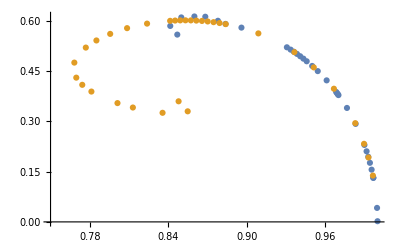

```mathematica
ListPlot[{sphivsswf,wfvsm0},Joined->False,PlotRange->{{0.75,1},All}]
```

```mathematica
wfvsm0={{0.996518953639359,0.13817240968436997},{0.9931207177105825,0.19213370573749056},{0.9897261136265322,0.232895268010532},{0.9830297630699733,0.29451981452208675},{0.966693475676939,0.3972867475846118},{0.9513028191707283,0.46086140205023074},{0.9364991603249352,0.5063348552460164},{0.9089249484829022,0.5623291427706751},{0.8839540649030954,0.5900278719944302},{0.8792629731066395,0.5932669921965669},{0.8746722299517459,0.5958845385772668},{0.8701790720379096,0.5979421268535403},{0.8657853050155124,0.5994757313649417},{0.861488867698777,0.6005303637987167},{0.857289104983524,0.6011441981697094},{0.8531871409916418,0.6013504355995851},{0.8491810473335771,0.6011800529477211},{0.845270983444457,0.6006604130529007},{0.8414566266748835,0.599817165082971},{0.8238113468576457,0.5915176837572068},{0.8085304979793462,0.5779929618736941},{0.7956144269475499,0.5608565659827082},{0.7850816256396899,0.5412562911286998},{0.7769689974674016,0.5200347892934782},{0.7682038195058204,0.4751977105326323},{0.7696821230471831,0.43033244823998784},{0.7742622314362726,0.4089435260603959},{0.781258310292559,0.3888299271450409},{0.8011941306750231,0.354414335684311},{0.8129624820561271,0.3412110586578644},{0.8356570548394765,0.3254645238261879},{0.8548810393351576,0.3298533015467182},{0.8479228589860571,0.35976607365984564}};
```

```mathematica
XXeta032=Interpolation[sphivsswf,InterpolationOrder->2, Method->"Spline"];
```

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

```mathematica
XXeta03=Interpolation[sphivsswf,InterpolationOrder->2, Method->"Spline"];
```

```mathematica
XXeta03mvsr=Interpolation[mvsr,InterpolationOrder->2, Method->"Spline"];
```

InterpolatingFunction::dmval: Input value {0.835003} lies outside the range of data in the interpolating function. Extrapolation will be used.

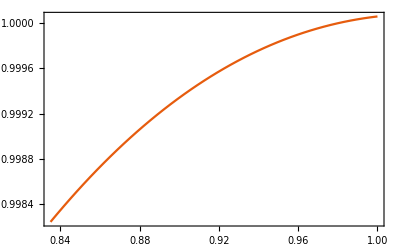

```mathematica
Show[Plot[{XXeta032[w]},{w,0.835,1},PlotTheme->"Scientific"],ListPlot[sphivsswf]]
```

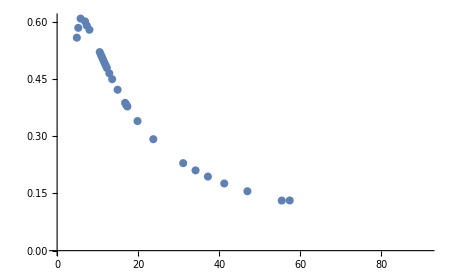

```mathematica
ListPlot[mvsr]
```

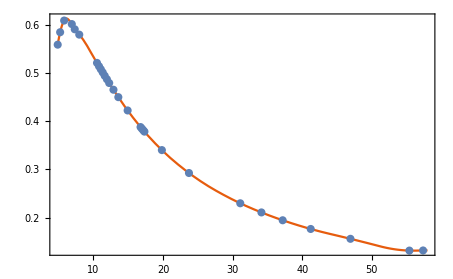

```mathematica
Show[Plot[XXeta03mvsr[R],{R,4.8,58},PlotTheme->"Scientific"],ListPlot[mvsr]]
```

```mathematica
wvsM95={};
Do[AppendTo[wvsM95,{w,XXeta03[w]}],{w,0.835,1,0.002}]
```

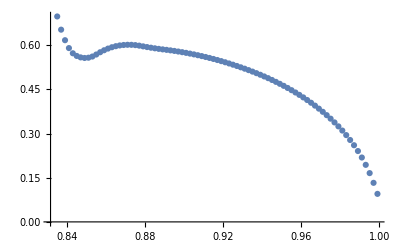

```mathematica
ListPlot[wvsM95,PlotRange->All]
```

```mathematica
Export["Dat_wvsM95_etam03.dat",wvsM95]
```

Dat_wvsM95_etam03.dat

```mathematica
mvsr={};
Do[AppendTo[mvsr,{R,XXeta03mvsr[R]}],{R,4.8,55,0.1}]
```

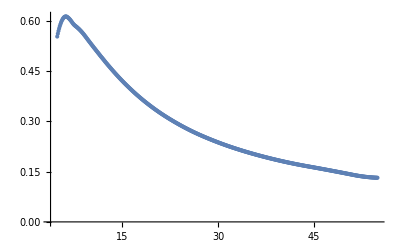

```mathematica
ListPlot[mvsr,PlotRange->All]
```

```mathematica
Export["Dat_mvsr_etam03.dat",mvsr]
```

Dat_mvsr_etam03.dat

```mathematica
wvsM95=Import["Dat_wvsM95_etam03.dat"]
```

{{0.835,0.697643},{0.837,0.652791},{0.839,0.617002},{0.841,0.590276},{0.843,0.572613},{0.845,0.563568},{0.847,0.55864},{0.849,0.55666},{0.851,0.557629},{0.853,0.561546},{0.855,0.568411},{0.857,0.576169},{0.859,0.582877},{0.861,0.588536},{0.863,0.593146},{0.865,0.596706},{0.867,0.599217},{0.869,0.600753},{0.871,0.60145},{0.873,0.60131},{0.875,0.600333},{0.877,0.598519},{0.879,0.596072},{0.881,0.593715},{0.883,0.591514},{0.885,0.589469},{0.887,0.587579},{0.889,0.585845},{0.891,0.584221},{0.893,0.582476},{0.895,0.58058},{0.897,0.578533},{0.899,0.576335},{0.901,0.573985},{0.903,0.571483},{0.905,0.568831},{0.907,0.566027},{0.909,0.563071},{0.911,0.559965},{0.913,0.556707},{0.915,0.553295},{0.917,0.549724},{0.919,0.545993},{0.921,0.542103},{0.923,0.538054},{0.925,0.533846},{0.927,0.529478},{0.929,0.524951},{0.931,0.520265},{0.933,0.515416},{0.935,0.510371},{0.937,0.505142},{0.939,0.499683},{0.941,0.493962},{0.943,0.488135},{0.945,0.481968},{0.947,0.475544},{0.949,0.468919},{0.951,0.462014},{0.953,0.454815},{0.955,0.447306},{0.957,0.439483},{0.959,0.431332},{0.961,0.422803},{0.963,0.413892},{0.965,0.404597},{0.967,0.394841},{0.969,0.384576},{0.971,0.373818},{0.973,0.362495},{0.975,0.350554},{0.977,0.337865},{0.979,0.324424},{0.981,0.310173},{0.983,0.294775},{0.985,0.278176},{0.987,0.260361},{0.989,0.24064},{0.991,0.218638},{0.993,0.193744},{0.995,0.165662},{0.997,0.132652},{0.999,0.0951655}}

```mathematica
ListPlot[wvsM95]
```

-Graphics-

## Test

```mathematica
Datm03={{0.0000100000000000000008180305391403130954586231382563710213`30.,1.00007812500000004164854225385816732796229189261794090271`30.,250.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0000900000000000000056682089577542171809909632429480552673`30.,1.0002929687500000416902840374988592486715788254514336585999`30.,250.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0008999999999999999753669266411293392593506723642349243164`30.,1.002941894531250056490998944641601653415818873327225446701`30.,90.061,30,-0.3,10^-3},{0.00092000000000000002782496455466798579436726868152618408203125`60.,1.003011718749999986628751447170770916272886097431182861328125`60.,100.061,60,-0.3,0.001`60.},{0.00129600000000000027677860003905152552761137485504150390625`60.,1.004250305175781218084449068761454526566012646071612834930419921875`60.,100.061,60,-0.3,0.001`60.},{0.00167200000000000009205136652923329165787436068058013916015625`60.,1.0054948730468749494505915909048354706101235933601856231689453125`60.,100.061,60,-0.3,0.001`60.},{0.002048000000000000341005002013616831391118466854095458984375`60.,1.006744514465331961990772198338450760246587378787808120250701904296875`60.,100.061,60,-0.3,0.001`60.},{0.0024240000000000003731182030008994843228720128536224365234375`60.,1.007999476432800204920042745214588120195031706316513009369373321533203125`60.,100.061,60,-0.3,0.001`60.},{0.0029100000000000002600697435184429195942357182502746582031`30.,1.0096290707588196387964010499137246495288122716260659217369`30.,90.061,30,-0.3,10^-3},{0.004920000000000000761612994892857386730611324310302734375`30.,1.0164625474950299276896850658824078646138742380161668066307`30.,90.061,30,-0.3,10^-3},{0.0069300000000000003957945082788683066610246896743774414062`30.,1.0234498030065879626115298317316712883946142239861929607025`30.,92.061,30,-0.3,10^-3},{0.0089400000000000017646994976416863210033625364303588867188`30.,1.030594532029044851005172410378025284137253304694696338234`30.,93.061,30,-0.3,10^-3},{0.0091000000000000004496403249731883988715708255767822265625`30.,1.0311701387532537614333723330074617653904393108735608691837`30.,90.061,30,-0.3,10^-3},{0.0092999999999999992394972281317677698098123073577880859375`30.,1.0318912281160010686235844299399885794567479507539281557982`30.,76.061,30,-0.3,10^-3},{0.0094999999999999997640776072671542351599782705307006835938`30.,1.0326138473246829316655783752630477362878949832347350024087`30.,75.061,30,-0.3,10^-3},{0.0118000000000000014599432773820808506570756435394287109375`30.,1.041041833898771098790348077080324265937301901488320126346`30.,75.061,30,-0.3,10^-3},{0.0140000000000000002914335439641035918612033128738403320312`30.,1.0493096643520403441406366802502799349343783698361790013287`30.,60.061,30,-0.3,10^-3},{0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3},{0.0167999999999999989619414719754786347039043903350830078125`50.,1.060134887695312553410509522067162180292143602855503559112548828125`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.01764000000000000289990254032090888358652591705322265625`50.,1.063449096679687556354118420365306718622377957217395305633544921875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.0184799999999999998989697047591107548214495182037353515625`50.,1.06679687500000005932754287840680262888781726360321044921875`50.,30.060100000000173,50,-0.3,0.0001`50.},{0.0193200000000000003674838211509268148802220821380615234375`50.,1.070175170898437562328072390760436150003442890010774135589599609375`50.,30.06010000000006,50,-0.3,0.0001`50.},{0.0201600000000000008359979375427428749389946460723876953125`50.,1.073587036132812565358417462857421043054273468442261219024658203125`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0210000000000000013045120539345589349977672100067138671875`50.,1.07703170776367194341790046833995386776905434089712798595428466796875`50.,30.060100000000045,50,-0.3,0.0001`50.},{0.021999999999999998723243521681069978512823581695556640625`50.,1.0811759948730469009490237457249417474258734728209674358367919921875`50.,30.060100000000073,50,-0.3,0.0001`50.},{0.0350000000000000033306690738754696212708950042724609375`50.,1.1396667480468749913155405983911094836003030650317668914794921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.040000000000000000832667268468867405317723751068115234375`50.,1.16466979980468747651075993310154643722853506915271282196044921875`50.,20.060010000000002,50,-0.3,1.`50.*^-5},{0.04499999999999999833466546306226518936455249786376953125`50.,1.1910937499999999476807399645394980325363576412200927734375`50.,14.060001,50,-0.3,1.`50.*^-6},

(*{0.04599999999999999922284388276239042170345783233642578125`30.,1.196343749999999976629805331640454824082553386688232421875`30.,12.060001,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},*)

(*{0.05000000000000000277555756156289135105907917022705078125`60.,1.21992187499999997328525846995717074605636298656463623046875`60.,11.060001,60,-0.3,1.`60.*^-6},*){0.059999999999999997779553950749686919152736663818359375`60.,1.280937500000000027478019859472624375484883785247802734375`60.,11.060001,60,-0.3,1.`60.*^-6},{0.061999999999999999555910790149937383830547332763671875`60.,1.2962500000000000410782519111307919956743717193603515625`60.,9.060001,60,-0.3,1.`60.*^-6},{0.064000000000000001332267629550187848508358001708984375`60.,1.314062500000000056898930012039272696711122989654541015625`60.,8.060001,60,-0.3,1.`60.*^-6}};
```

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,18,30,-0.3,10^-5};
```

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5};
```

```mathematica
Bs={0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3};
```

```mathematica
Bs={0.01400000000000000029143354396410359186120331287384033203125`60.,1.04929629802703851565280832578742897798207422965788282454013824462890625`60.,40.061,60,0.3,0.001`60.};
```

```mathematica
Bs={0.0140000000000000002914335439641035918612033128738403320312`30.,1.0493096643520403441406366802502799349343783698361790013287`30.,60.061,30,-0.3,10^-3};
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

r→9.058680.569905

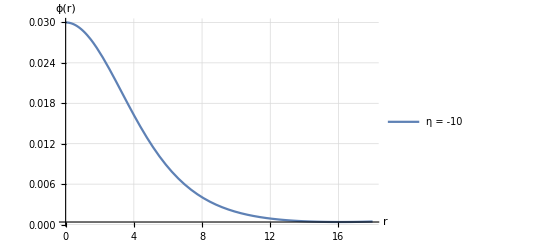

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=SetPrecision[Bs[[2]],prec];
rMax=SetPrecision[Bs[[3]],prec];
rMin=SetPrecision[Bs[[6]],prec];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]; 

M95=0.95M[rMax][[1]]; (* masa física *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];
Print[rad, M95];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

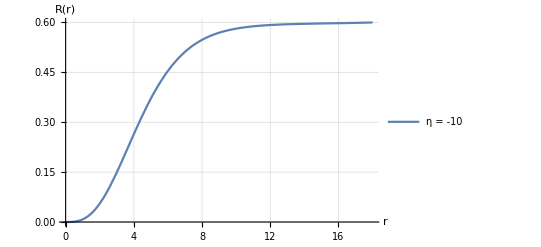

```mathematica
Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","R(r)"},
GridLines->Automatic]
```

```mathematica
(* sin la corrección *)
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s];
Masa=M[rMax][[1]]
```

0.5999

```mathematica
datos3={};
Do[AppendTo[datos3,{r,(Evaluate[gg[rm]/.s]/.rm-> r)[[1]]}],{r,rMin,rMax,0.01}]
```

```mathematica
Export["BHXXg03.dat",datos3]
```

BHXXg03.dat

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

-Graphics-

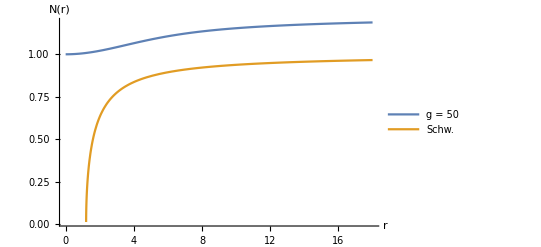

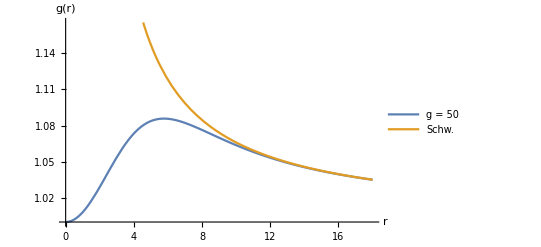

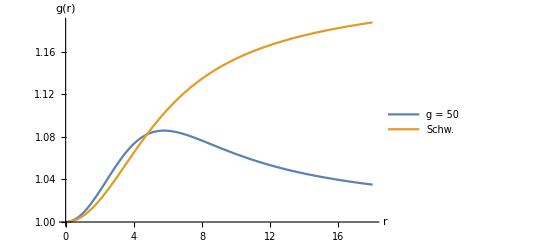

```mathematica
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->All,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]

Plot[{Evaluate[gg[r]/.s],Evaluate[NN[r]/.s]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,Evaluate[gg[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncN={};
Do[AppendTo[FuncN,{r,Evaluate[NN[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Funcsigma={};
Do[AppendTo[Funcsigma,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncM={};
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

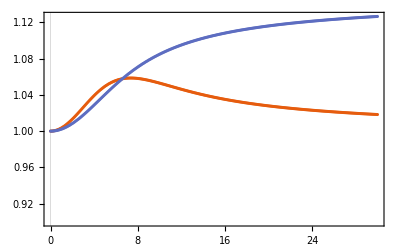

```mathematica
ListPlot[{Funcg,FuncN},PlotTheme->"Scientific",AxesOrigin->{0,0.9}, PlotRange->Automatic]
```

```mathematica
Export["FuncgM.dat",Funcg]
Export["FuncNM.dat",FuncN]
Export["FuncsigmaM.dat",Funcsigma]
```

```mathematica
Export["XX_2_masa_Profile_Pos.dat",FuncM]
Export["XX_2_sigma_Profile_Pos.dat",Funcsigma]
```

XX_2_masa_Profile_Pos.dat

XX_2_sigma_Profile_Pos.dat

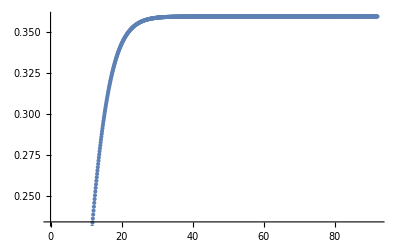

```mathematica
ListPlot[FuncM]
```

```mathematica
w2
```

0.954337

```mathematica
w
```

1.0735870361328125653584174628574210430542734684423

```mathematica
Clear[rMin,rTest,α,w,ϕ0,mS,k,η]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

(*AppendTo[SeidelBCList,{NN[rMin]==1*B[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)

AppendTo[SeidelBCList,{NN[rMin]==(1+(rMin^2 (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(6 (2 k+3 w^4 η ϕ0^4)^2))*B[[1,1,1,2]],gg[rMin]==1.+(rMin^2 ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(2 (6 k+9 w^4 η ϕ0^4)),φ[rMin]==ϕ0-0.5 rMin^2 w^2 ϕ0,NN'[rMin]==((rMin (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(3 (2 k+3 w^4 η ϕ0^4)^2))*B[[1,1,1,2]],gg'[rMin]==(rMin ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(6 k+9 w^4 η ϕ0^4),φ'[rMin]==-1. rMin w^2 ϕ0}]
```

{{NN[rMin]==0.814695 (1+(rMin^2 (-2 k (mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(6 (2 k+3 w^4 η ϕ0^4)^2)),gg[rMin]==1.+(rMin^2 ϕ0^2 (mS^2+w^2 α-24 w^6 η ϕ0^2))/(2 (6 k+9 w^4 η ϕ0^4)),φ[rMin]==ϕ0-0.5 rMin^2 w^2 ϕ0,NN'[rMin]==(0.271565 rMin (-2 k (mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/((2 k+3 w^4 η ϕ0^4)^2),gg'[rMin]==(rMin ϕ0^2 (mS^2+w^2 α-24 w^6 η ϕ0^2))/(6 k+9 w^4 η ϕ0^4),φ'[rMin]==-1. rMin w^2 ϕ0}}

```mathematica
w2
```

0.909196

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

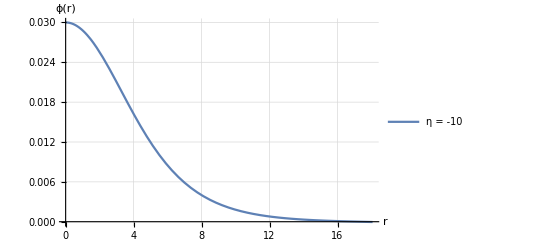

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=0.909192116376728(*w2 0.909192116376728*);
rMax=SetPrecision[Bs[[3]],prec];(*35*)
rMin=10^-4(*SetPrecision[Bs[[6]],prec]*);

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s];
Masa=M[rMax][[1]]
```

0.589944

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

-Graphics-

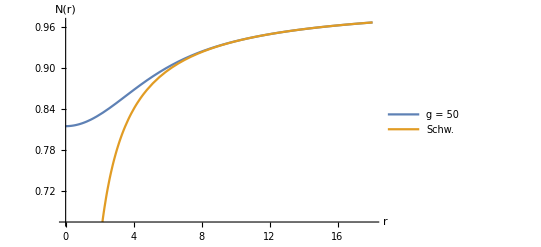

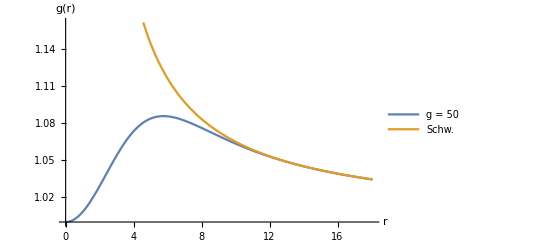

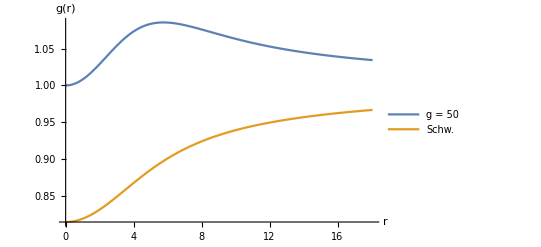

```mathematica
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->Automatic,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]

Plot[{Evaluate[gg[r]/.s],Evaluate[NN[r]/.s]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

Saved data

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,Evaluate[gg[r]/.s][[1]]}],{r,rMin,rMax,0.1}]

FuncN={};
Do[AppendTo[FuncN,{r,Evaluate[NN[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncM={};
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

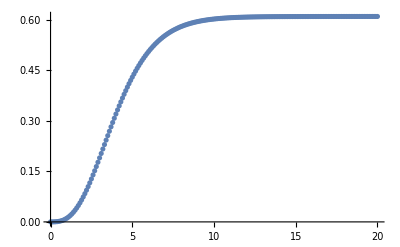

```mathematica
ListPlot[FuncM]
```

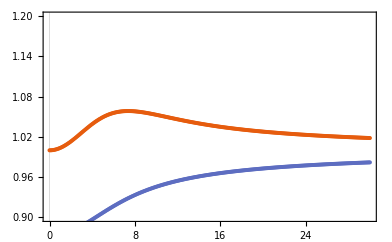

```mathematica
ListPlot[{Funcg,FuncN},PlotTheme->"Scientific",AxesOrigin->{0,0.9},PlotRange->{All,{0.9,1.2}}]
```

```mathematica
Export["Funcg.dat",Funcg]
Export["FuncN.dat",FuncN]
```

Funcg.dat

FuncN.dat

```mathematica
Export["FuncM.dat",FuncM]
```

FuncM.dat

```mathematica
Evaluate[Van[r]/.s]/.r-> 12.879215326320738
```

{2.0506×10^-9}

```mathematica
Evaluate[Van[r]/.s]/.r->9.058677580711654
```

{1.45622×10^-8}

```mathematica
Log10[1.4562150374430871*^-8]
```

-7.83677

```mathematica
{9.058677580711654,(Evaluate[Log10@Van[r]/.s]/.r->9.058677580711654)[[1]]}
```

{9.05868,-7.83677}

```mathematica
den[r_]:=(gg[r]^4 NN[r]^4)/(gg[r]^4 NN[r]^4+440π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)^2);
```

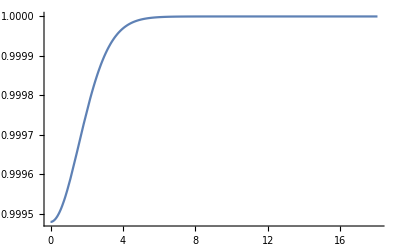

```mathematica
Plot[Evaluate[den[r]/.s],{r,rMin,rMax},PlotRange->All]
```

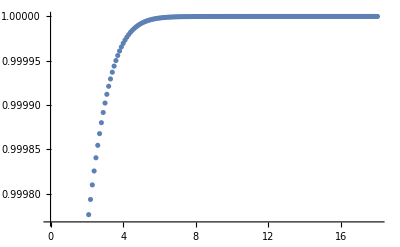

```mathematica
FuncD={};
Do[AppendTo[FuncD,{r, (Evaluate[den[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,rMax,0.1}]
ListPlot[FuncD]
```

```mathematica
η
```

-0.3

```mathematica
Export["EtaP.dat",FuncD]
```

EtaP.dat

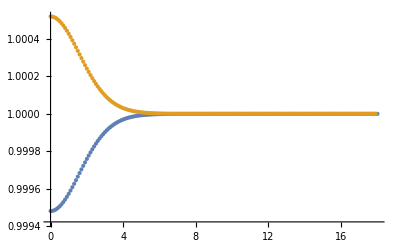

```mathematica
Pos=Import["EtaP.dat"];
Neg=Import["EtaN.dat"];

ListPlot[{Pos,Neg},PlotRange->All]
```

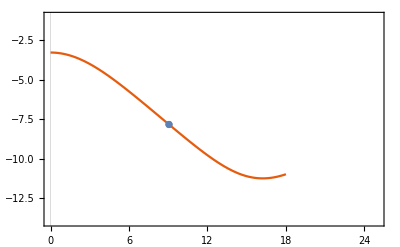

```mathematica
Van[r_]:=Abs[1-(gg[r]^4 NN[r]^4)/(gg[r]^4 NN[r]^4+440π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)^2)];(*Subscript[G, N]/G*)

Show[{Plot[{Evaluate[Log10@Van[r]/.s]},{r,rMin,rMax}, PlotRange->{{0,25},{-14,-1}},AxesOrigin->{0,0},PlotTheme->"Scientific"],ListPlot[{{9.058677580711654,(Evaluate[Log10@Van[r]/.s]/.r->9.058677580711654)[[1]]}}]}]
```

```mathematica
a=Import["VanisXX_1.dat"];
```

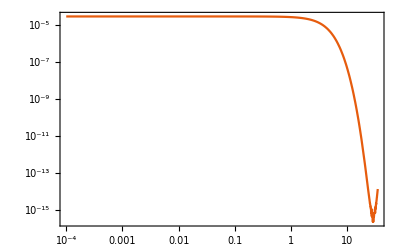

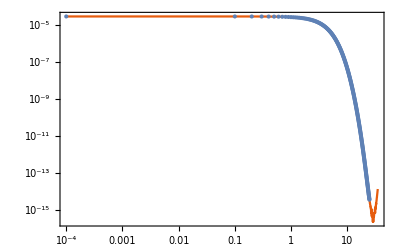

```mathematica
b=LogLogPlot[Evaluate[Van[r]/.s],{r,rMin,rMax},AxesOrigin->{0,0},PlotRange->All,PlotTheme->"Scientific"]
c=ListLogLogPlot[a];
Show[{b,c}]
```

```mathematica
FindRoot[Evaluate[Log10@Van[r]/.s][[1]]==-4.327902142064283,{r,1}]
```

{r→3.654}

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,(Evaluate[Van[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,rMax,0.1}]
```

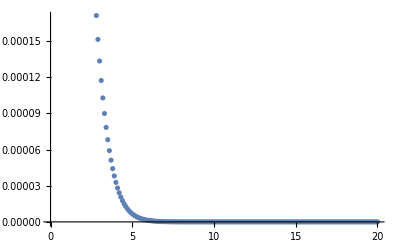

```mathematica
ListPlot[Funcg]
```

```mathematica
Export["VanisXX_2.dat",Funcg]
```

VanisXX_2.dat

## Generando datos

```mathematica
A[r_,η_,w_]=1/(1+440π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)^2/(gg[r]^4 NN[r]^4));
```

```mathematica
Clear[η,w]
```

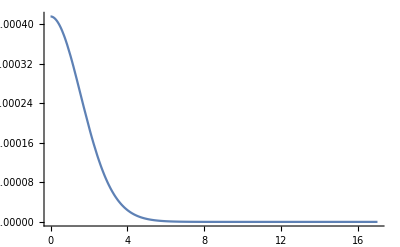

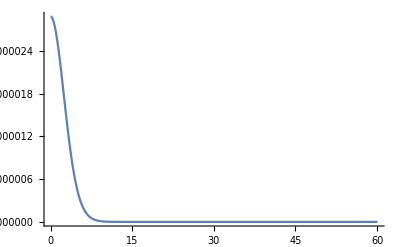

```mathematica
a=Plot[Evaluate[A[r,0.3,0.909196]/.sP],{r,rMin,17},PlotRange->All]
b=Plot[Evaluate[A[r,-0.3,0.908042]/.sN],{r,rMin,rMax},PlotRange->All]
```

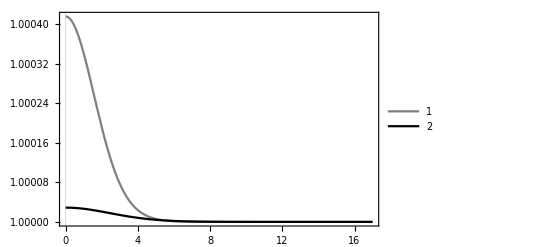

```mathematica
Plot[{Evaluate[A[r,0.3,0.909196]/.sP],Evaluate[A[r,-0.3,0.908042]/.sN]},{r,rMin,17},PlotRange->All,PlotStyle->{Gray,Black},PlotTheme->"Scientific",PlotLegends->Automatic]
```

```mathematica
1/Evaluate[A[rMin,0.3,0.909196]/.sN]
```

{1.00003}

{1.00042}

```mathematica
{0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5}
```

```mathematica
{0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,18,30,-0.3,10^-5}
```

```mathematica
{0.03,1.116036581602133000,30,50,0,10^-3}
```

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,17,60,0.3,1.`60.*^-5};(*{0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3}*)(*Datm03[[-10]]*);
```

```mathematica
Bs={0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3};
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

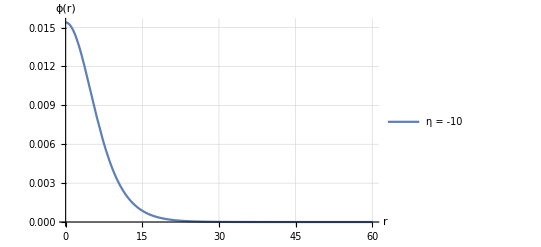

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=SetPrecision[Bs[[2]],prec];
rMax=SetPrecision[Bs[[3]],prec];
rMin=SetPrecision[Bs[[6]],prec];

sN=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

Plot[{Evaluate[φ[r]/.sN]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

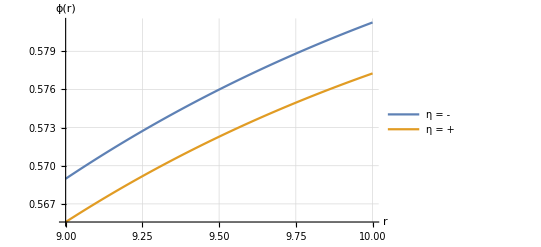

```mathematica
Plot[{Evaluate[M[r]/.s],Evaluate[M[r]/.sP]},{r,9,10},
Background->White,PlotLegends->Placed[{"η = -" (*, "η = 0.01","η = 0.1"*), "η = +","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

```mathematica
Funcphi={};
FuncM={};
Do[AppendTo[Funcphi,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

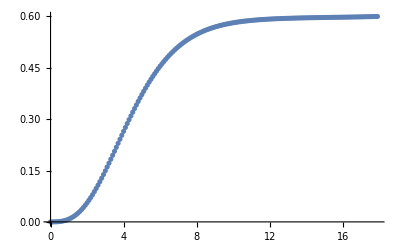

```mathematica
ListPlot[FuncM]
```

```mathematica
w2
```

0.908042

```mathematica
Evaluate[M[rMax]/.s][[1]]
```

0.5999

```mathematica
0.95*%
```

0.569905

0.560421

```mathematica
{0.9091962116376728,0.5604212624159505},{0.9080424976269752,0.5699054566272543}
```

```mathematica
η
```

-0.3

```mathematica
Export["XX_2_sigma_Profile.dat",Funcphi]
Export["XX_2_masa_Profile.dat",FuncM]
```

XX_2_sigma_Profile.dat

XX_2_masa_Profile.dat

## Test

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`30.,1.115996093750000050549842089964158731163479387760162353515625`60.,18,30,-0.3,10^-5};
```

```mathematica
Bs={0.0299999999999999988897769753748434595763683319091796875`60.,1.115996093750000050549842089964158731163479387760162353515625`60.,18.06001,60,0.3,1.`60.*^-5};
```

0.909196

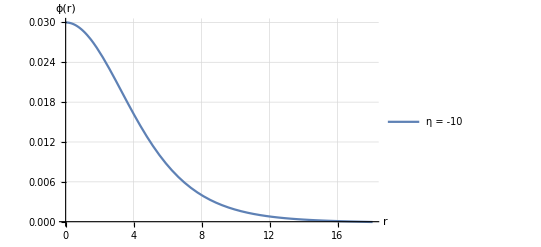

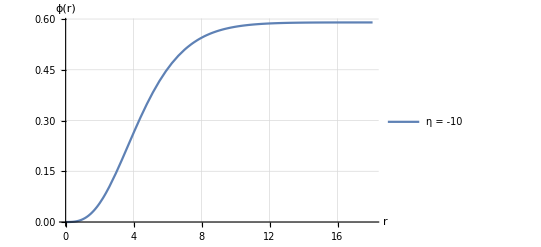

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=Bs[[1]];
w=Bs[[2]];
rMax=Bs[[3]];
rMin=Bs[[6]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}, MaxSteps->10^6];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];

Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
Clear[rMin,rTest,α,w,ϕ0,mS,k,η]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

(*AppendTo[SeidelBCList,{NN[rMin]==1*B[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)

AppendTo[SeidelBCList,{NN[rMin]==(1+(rMin^2 (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(6 (2 k+3 w^4 η ϕ0^4)^2))*B[[1,1,1,2]],gg[rMin]==1.+(rMin^2 ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(2 (6 k+9 w^4 η ϕ0^4)),φ[rMin]==ϕ0-0.5 rMin^2 w^2 ϕ0,NN'[rMin]==((rMin (-2 k (L1 mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 L1 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(3 (2 k+3 w^4 η ϕ0^4)^2))*B[[1,1,1,2]],gg'[rMin]==(rMin ϕ0^2 (L1 mS^2+w^2 α-24 w^6 η ϕ0^2))/(6 k+9 w^4 η ϕ0^4),φ'[rMin]==-1. rMin w^2 ϕ0}]
```

{{NN[rMin]==0.814695 (1+(rMin^2 (-2 k (mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/(6 (2 k+3 w^4 η ϕ0^4)^2)),gg[rMin]==1.+(rMin^2 ϕ0^2 (mS^2+w^2 α-24 w^6 η ϕ0^2))/(2 (6 k+9 w^4 η ϕ0^4)),φ[rMin]==ϕ0-0.5 rMin^2 w^2 ϕ0,NN'[rMin]==(0.271565 rMin (-2 k (mS^2-2 w^2 α) ϕ0^2+w^4 η ϕ0^6 (-5 mS^2+4 w^2 α+48 w^6 η ϕ0^2)))/((2 k+3 w^4 η ϕ0^4)^2),gg'[rMin]==(rMin ϕ0^2 (mS^2+w^2 α-24 w^6 η ϕ0^2))/(6 k+9 w^4 η ϕ0^4),φ'[rMin]==-1. rMin w^2 ϕ0}}

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=0.909192116376728(*w2 0.909192116376728*);
rMax=SetPrecision[Bs[[3]],prec];(*35*)
rMin=10^-4(*SetPrecision[Bs[[6]],prec]*);

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

-Graphics-

```mathematica
(* Ploteando la función lapso *)
Masa=Evaluate[M[rMax]/.s];
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->Automatic,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

-Graphics-

-Graphics-

```mathematica
den[r_]:=gg[r]^4 NN[r]^4+440π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)^2;
```

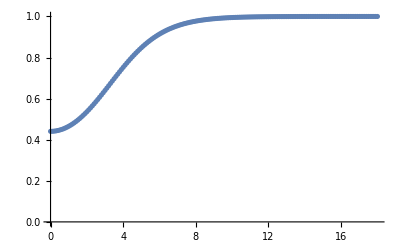

```mathematica
FuncD={};
Do[AppendTo[FuncD,{r, (Evaluate[den[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,rMax,0.1}]
ListPlot[FuncD]
```

```mathematica
η
```

0.3

```mathematica
Export["BEtaP.dat",FuncD]
```

BEtaP.dat

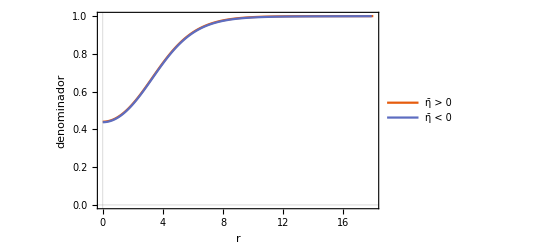

```mathematica
Pos=Import["BEtaP.dat"];
Neg=Import["BEtaN.dat"];

ListPlot[{Pos,Neg},PlotTheme->"Scientific",Joined->True,FrameLabel->{"r"," denominador"},PlotLegends->Placed[{"η̄ > 0", "η̄ < 0"},{0.75,0.45}]]
```

```mathematica
Van[r_]:=(gg[r]^4 NN[r]^4)/(gg[r]^4 NN[r]^4+440π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)^2);
```

```mathematica
FuncD2={};
Do[AppendTo[FuncD2,{r, (Evaluate[Van[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,rMax,0.1}]
ListPlot[FuncD2]
```

-Graphics-

```mathematica
Export["TestBEtaP.dat",FuncD2]
```

TestBEtaP.dat

```mathematica
TPos=Import["TestBEtaP.dat"];
TNeg=Import["TestBEtaN.dat"];
```

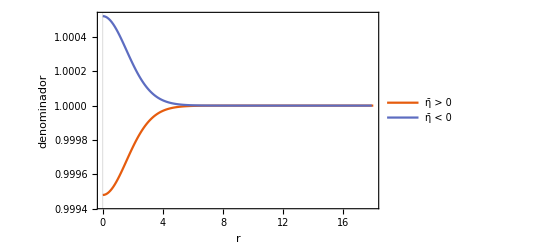

```mathematica
ListPlot[{TPos,TNeg},PlotRange->All,PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameLabel->{"r"," denominador"},PlotLegends->Placed[{"η̄ > 0", "η̄ < 0"},{0.75,0.75}]]
```